```mathematica
s="8 5 4 9 2 1 28 
8 1 9 5 18 
8 9 5 1 4 2 6 28 
8 28 
8 1 9 5 18 
8 5 2 7 4 1 9 6 3 0 22 
8 9 1 5 4 2 28 
8 28 
8 1 9 5 7 2 18 
8 1 9 2 5 28 
8 1 9 5 18 
8 1 9 5 4 0 22 
8 28 
8 1 9 5 28 
8 1 9 2 5 28 
8 1 9 5 4 0 22 
8 1 9 5 0 22 
8 1 9 5 28 
8 28 
8 1 9 5 18 
8 5 4 9 2 1 28 
8 9 1 5 2 4 7 6 3 0 22 
8 28 
8 1 9 2 5 28 
8 28 
8 5 7 4 2 1 9 6 0 22 
8 1 9 0 2 5 28 
8 5 22 
8 1 9 5 18 
8 1 9 5 28 
8 1 9 2 5 28 
8 1 9 2 5 7 4 18 
8 1 9 5 4 0 22 
8 1 9 5 0 22 
8 1 9 5 18 
8 5 22 
8 1 9 2 5 28 
8 1 9 5 28 
8 1 9 5 28 
8 1 9 5 18 
8 28 
8 5 4 1 2 6 9 23 
8 1 9 2 5 28 
8 28 
8 1 9 5 28 
8 28 
8 28 
8 28 
8 1 9 5 18 
8 1 9 5 28 
8 1 9 2 5 28 
8 1 9 5 18 
8 1 9 5 4 2 7 6 0 18 
8 1 9 5 18 
8 1 9 2 5 28 
8 28 
8 28 
8 5 22 
8 1 9 2 5 28 
8 1 9 5 28 
8 5 22 
8 5 18 
8 1 9 5 18 
8 28 
8 5 4 2 9 7 1 0 22 
8 5 9 4 1 28 
8 1 9 5 0 22 
8 28 
8 28 
8 1 9 5 18 
8 1 9 5 18 
8 5 4 7 9 2 1 6 3 0 22 
8 1 9 5 2 7 
8 9 1 5 18 
8 1 9 0 22 
8 1 9 2 5 28 
8 28 
8 1 9 5 18 
8 1 9 5 0 22 
8 28 
8 1 9 5 18 
8 1 9 5 18 
8 1 9 5 18 
8 28 
8 1 9 2 5 28 
8 28 
8 1 9 0 22 
8 5 7 4 2 1 9 0 22 
8 1 9 2 5 28 
8 28 
8 9 1 5 2 4 7 6 0 22 
8 28 
8 1 9 5 18 
8 1 9 0 22 
8 1 9 2 5 28 
8 9 1 5 2 7 4 6 3 0 22 
8 1 9 2 5 28 
8 28 
8 28";
```

```mathematica
data=Map[ToExpression[StringSplit[#," "]]&,StringSplit[s,"\n"]];
```

```mathematica
f[row_]:=Join[row⟦1;;-2⟧,{"S_"<>ToString[row⟦-1⟧]}]
```

```mathematica
fdata=Map[f,data];
```

```mathematica
edges[a_]:=Table[a⟦i⟧->a⟦i+1⟧,{i,1,Length[a]-1}]
```

```mathematica
stye[s_][e_]:=Style[e,Colors]
```

```mathematica
cf=ColorData["Rainbow"];
```

```mathematica
stye[Blue][start⟦1,1⟧]
```

3->1

```mathematica
start=RandomSample[Map[edges,fdata]]
```

{{8->1,1->9,9->0,0->S_22},{8->5,5->S_22},{8->1,1->9,9->0,0->S_22},{8->9,9->1,1->5,5->S_18},{8->9,9->1,1->5,5->2,2->7,7->4,4->6,6->3,3->0,0->S_22},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->2,2->5,5->S_28},{8->5,5->S_18},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->5,5->S_28},{8->S_28},{8->1,1->9,9->2,2->5,5->7,7->4,4->S_18},{8->S_28},{8->S_28},{8->S_28},{8->5,5->4,4->2,2->9,9->7,7->1,1->0,0->S_22},{8->1,1->9,9->5,5->S_18},{8->9,9->1,1->5,5->2,2->4,4->7,7->6,6->0,0->S_22},{8->1,1->9,9->5,5->S_18},{8->S_28},{8->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->1,1->9,9->5,5->S_28},{8->1,1->9,9->5,5->S_28},{8->1,1->9,9->5,5->4,4->0,0->S_22},{8->S_28},{8->1,1->9,9->5,5->S_18},{8->9,9->1,1->5,5->4,4->2,2->S_28},{8->5,5->7,7->4,4->2,2->1,1->9,9->0,0->S_22},{8->1,1->9,9->5,5->7,7->2,2->S_18},{8->S_28},{8->S_28},{8->1,1->9,9->5,5->0,0->S_22},{8->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->1,1->9,9->5,5->4,4->0,0->S_22},{8->1,1->9,9->5,5->4,4->0,0->S_22},{8->1,1->9,9->5,5->S_18},{8->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->5,5->2,2->7,7->4,4->1,1->9,9->6,6->3,3->0,0->S_22},{8->5,5->S_22},{8->S_28},{8->1,1->9,9->5,5->S_28},{8->5,5->4,4->7,7->9,9->2,2->1,1->6,6->3,3->0,0->S_22},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->5,5->0,0->S_22},{8->1,1->9,9->2,2->5,5->S_28},{8->1,1->9,9->0,0->S_22},{8->1,1->9,9->5,5->S_28},{8->1,1->9,9->5,5->S_28},{8->1,1->9,9->5,5->S_28},{8->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->S_28},{8->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->S_28},{8->1,1->9,9->5,5->2,2->S_7},{8->S_28},{8->1,1->9,9->0,0->2,2->5,5->S_28},{8->1,1->9,9->5,5->0,0->S_22},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->2,2->5,5->S_28},{8->5,5->4,4->9,9->2,2->1,1->S_28},{8->S_28},{8->S_28},{8->S_28},{8->S_28},{8->9,9->5,5->1,1->4,4->2,2->6,6->S_28},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->5,5->S_18},{8->S_28},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->5,5->S_18},{8->5,5->7,7->4,4->2,2->1,1->9,9->6,6->0,0->S_22},{8->1,1->9,9->2,2->5,5->S_28},{8->1,1->9,9->5,5->S_28},{8->1,1->9,9->5,5->0,0->S_22},{8->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->5,5->S_22},{8->5,5->4,4->1,1->2,2->6,6->9,9->S_23},{8->S_28},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->2,2->5,5->S_28},{8->1,1->9,9->5,5->S_18},{8->5,5->S_22},{8->5,5->4,4->9,9->2,2->1,1->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->1,1->9,9->2,2->5,5->S_28},{8->1,1->9,9->5,5->4,4->2,2->7,7->6,6->0,0->S_18},{8->9,9->1,1->5,5->2,2->4,4->7,7->6,6->3,3->0,0->S_22},{8->1,1->9,9->2,2->5,5->S_28},{8->5,5->9,9->4,4->1,1->S_28},{8->1,1->9,9->5,5->S_18},{8->1,1->9,9->5,5->S_18}}

```mathematica
cs=Flatten[Table[Map[cf[s/Length[start]]&,start⟦s⟧],{s,1,Length[start]}]];
```

```mathematica
es = Flatten[start];
```

```mathematica
{es2,cs2}=Transpose[SortBy[Transpose[{es,cs}],First]];
```

```mathematica
end=Table[Map[stye[cf[s/Length[start]]],start⟦s⟧],{s,1,Length[start]}];
```

```mathematica
i=1;

Export["ddqn_color.svg",Graph[es2,EdgeShapeFunction->({Arrowheads[Large],Thick,cs2⟦i++⟧,Arrow@#}&),VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding",ImageSize->Large]]
```

ddqn_color.svg

```mathematica
es
```

{3->S_28,3->S_19,3->S_18,3->S_17,3->S_24,3->S_20,3->S_28}

```mathematica
Length[start]
```

99

```mathematica
Flatten[start]
```

{3->S_25,3->0,0->6,6->2,2->S_6,3->S_23,3->S_4,3->S_18,3->S_13,3->4,4->S_13,3->S_28,3->S_21,3->8,8->1,1->S_10,3->7,7->8,8->5,5->S_10,3->S_18,3->S_23,3->7,7->8,8->1,1->S_2,3->8,8->S_28,3->S_17,3->S_4,3->S_30,3->2,2->0,0->1,1->S_5,3->S_28,3->8,8->1,1->2,2->9,9->S_15,3->S_0,3->S_4,3->S_13,3->S_22,3->S_10,3->S_24,3->S_14,3->S_2,3->S_5,3->S_18,3->S_21,3->S_8,3->S_30,3->6,6->4,4->S_18,3->S_30,3->S_4,3->S_10,3->S_19,3->S_17,3->5,5->S_13,3->1,1->6,6->9,9->S_25,3->S_24,3->4,4->S_19,3->S_7,3->S_14,3->S_7,3->7,7->S_12,3->S_8,3->S_18,3->S_13,3->S_12,3->S_16,3->7,7->8,8->5,5->1,1->S_4,3->9,9->S_26,3->S_14,3->S_20,3->S_27,3->S_2,3->S_5,3->S_27,3->S_28,3->8,8->0,0->6,6->S_24,3->S_9,3->4,4->S_20,3->0,0->1,1->S_27,3->0,0->1,1->S_28,3->S_0,3->S_2,3->5,5->2,2->1,1->S_11,3->6,6->S_12,3->S_24,3->S_15,3->6,6->7,7->S_21,3->S_13,3->S_5,3->1,1->6,6->S_28,3->S_20,3->S_10,3->S_4,3->S_23,3->S_4,3->S_10,3->S_2,3->S_3,3->S_12,3->S_17,3->S_17,3->S_24,3->8,8->S_26,3->S_28,3->S_1,3->6,6->S_29,3->S_18,3->S_15,3->S_5,3->S_28,3->7,7->S_13,3->S_13,3->S_18}

```mathematica
styles
```

{RGBColor[0.44575568, 0.11017624000000001, 0.54900848],RGBColor[0.42009936, 0.11158648, 0.57100096],RGBColor[0.39444304, 0.11299672000000001, 0.59299344],RGBColor[0.36878672, 0.11440696, 0.61498592],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.31747408, 0.11722744, 0.65897088],RGBColor[0.30382016, 0.13051672, 0.67703096]}

```mathematica
i
```

153

```mathematica
cs
```

{RGBColor[0.44575568, 0.11017624000000001, 0.54900848],RGBColor[0.42009936, 0.11158648, 0.57100096],RGBColor[0.42009936, 0.11158648, 0.57100096],RGBColor[0.42009936, 0.11158648, 0.57100096],RGBColor[0.42009936, 0.11158648, 0.57100096],RGBColor[0.39444304, 0.11299672000000001, 0.59299344],RGBColor[0.36878672, 0.11440696, 0.61498592],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.31747408, 0.11722744, 0.65897088],RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.29416704, 0.14776568, 0.6937802399999999],RGBColor[0.28451392, 0.16501464, 0.7105295199999999],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.26520768, 0.19951256, 0.74402808],RGBColor[0.26520768, 0.19951256, 0.74402808],RGBColor[0.26520768, 0.19951256, 0.74402808],RGBColor[0.26520768, 0.19951256, 0.74402808],RGBColor[0.25555456, 0.21676152, 0.76077736],RGBColor[0.25019616, 0.23625448, 0.7729065599999999],RGBColor[0.24913248, 0.25799144, 0.78041568],RGBColor[0.24913248, 0.25799144, 0.78041568],RGBColor[0.24913248, 0.25799144, 0.78041568],RGBColor[0.24913248, 0.25799144, 0.78041568],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.24700512, 0.30146536, 0.79543392],RGBColor[0.24594143999999998, 0.32320232, 0.80294304],RGBColor[0.24487776, 0.34493928, 0.81045216],RGBColor[0.24496168, 0.36625888, 0.8155418],RGBColor[0.24496168, 0.36625888, 0.8155418],RGBColor[0.24496168, 0.36625888, 0.8155418],RGBColor[0.24496168, 0.36625888, 0.8155418],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.25201512, 0.40639392, 0.8112042],RGBColor[0.25201512, 0.40639392, 0.8112042],RGBColor[0.25201512, 0.40639392, 0.8112042],RGBColor[0.25201512, 0.40639392, 0.8112042],RGBColor[0.25201512, 0.40639392, 0.8112042],RGBColor[0.25554184, 0.42646143999999997, 0.8090354000000001],RGBColor[0.25906856, 0.44652896, 0.8068666],RGBColor[0.26259528000000004, 0.46659648, 0.8046978],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.27248952000000004, 0.50248976, 0.7924709200000001],RGBColor[0.27885704, 0.51831552, 0.78241284],RGBColor[0.28522456, 0.5341412799999999, 0.77235476],RGBColor[0.29159208000000003, 0.54996704, 0.7622966800000001],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.30432712, 0.5816185599999999, 0.74218052],RGBColor[0.31246632, 0.59399708, 0.72838912],RGBColor[0.32119608, 0.60522652, 0.7133532800000001],RGBColor[0.32992584, 0.6164559599999999, 0.6983174400000001],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.34738536000000003, 0.63891484, 0.66824576],RGBColor[0.35611512, 0.65014428, 0.65320992],RGBColor[0.36602896, 0.6594462, 0.63726232],RGBColor[0.37712688, 0.6668206, 0.6204029600000001],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.39932272, 0.6815694, 0.5866842400000001],RGBColor[0.39932272, 0.6815694, 0.5866842400000001],RGBColor[0.41042064, 0.6889438, 0.5698248800000001],RGBColor[0.41042064, 0.6889438, 0.5698248800000001],RGBColor[0.41042064, 0.6889438, 0.5698248800000001],RGBColor[0.41042064, 0.6889438, 0.5698248800000001],RGBColor[0.42151856, 0.6963182, 0.5529655200000001],RGBColor[0.433185, 0.7029718399999999, 0.53633544],RGBColor[0.433185, 0.7029718399999999, 0.53633544],RGBColor[0.446557, 0.7074632, 0.5203932],RGBColor[0.45992900000000003, 0.71195456, 0.50445096],RGBColor[0.473301, 0.71644592, 0.48850872],RGBColor[0.486673, 0.72093728, 0.47256648],RGBColor[0.486673, 0.72093728, 0.47256648],RGBColor[0.500045, 0.72542864, 0.45662424],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.52849444, 0.7321276800000001, 0.42754696000000003],RGBColor[0.54357188, 0.73433536, 0.41441192000000004],RGBColor[0.55864932, 0.73654304, 0.40127688],RGBColor[0.57372676, 0.73875072, 0.38814184],RGBColor[0.57372676, 0.73875072, 0.38814184],RGBColor[0.57372676, 0.73875072, 0.38814184],RGBColor[0.57372676, 0.73875072, 0.38814184],RGBColor[0.57372676, 0.73875072, 0.38814184],RGBColor[0.5888042, 0.7409584, 0.37500680000000003],RGBColor[0.5888042, 0.7409584, 0.37500680000000003],RGBColor[0.60388164, 0.74316608, 0.36187176],RGBColor[0.61933744, 0.74358276, 0.35145748000000004],RGBColor[0.63491936, 0.74340244, 0.34195012],RGBColor[0.6505012800000001, 0.74322212, 0.33244276],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.68166512, 0.74286148, 0.31342804],RGBColor[0.69724704, 0.74268116, 0.30392068],RGBColor[0.7121988800000001, 0.74087636, 0.29609996],RGBColor[0.7121988800000001, 0.74087636, 0.29609996],RGBColor[0.7121988800000001, 0.74087636, 0.29609996],RGBColor[0.7121988800000001, 0.74087636, 0.29609996],RGBColor[0.72652064, 0.73744708, 0.28996588],RGBColor[0.7408424, 0.7340177999999999, 0.2838318],RGBColor[0.7408424, 0.7340177999999999, 0.2838318],RGBColor[0.75516416, 0.73058852, 0.27769772],RGBColor[0.75516416, 0.73058852, 0.27769772],RGBColor[0.75516416, 0.73058852, 0.27769772],RGBColor[0.7694859199999999, 0.72715924, 0.27156364],RGBColor[0.7694859199999999, 0.72715924, 0.27156364],RGBColor[0.7694859199999999, 0.72715924, 0.27156364],RGBColor[0.78380768, 0.72372996, 0.26542955999999995],RGBColor[0.7973075199999999, 0.71914252, 0.2598584],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8193756799999999, 0.70301868, 0.2520936],RGBColor[0.8193756799999999, 0.70301868, 0.2520936],RGBColor[0.83040976, 0.69495676, 0.2482112],RGBColor[0.8414438399999999, 0.68689484, 0.24432879999999998],RGBColor[0.8524779199999999, 0.67883292, 0.2404464],RGBColor[0.8524779199999999, 0.67883292, 0.2404464],RGBColor[0.8524779199999999, 0.67883292, 0.2404464],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.86951232, 0.6566998, 0.23336048],RGBColor[0.87551264, 0.6426286, 0.23015696],RGBColor[0.87551264, 0.6426286, 0.23015696],RGBColor[0.87551264, 0.6426286, 0.23015696],RGBColor[0.88151296, 0.6285573999999999, 0.22695344],RGBColor[0.88751328, 0.6144862, 0.22374992000000002],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.89951392, 0.5863438, 0.21734288000000002],RGBColor[0.90123468, 0.56736256, 0.21359864],RGBColor[0.90152892, 0.54674464, 0.20967416],RGBColor[0.90182316, 0.5261267199999999, 0.20574968],RGBColor[0.9021174, 0.5055088, 0.2018252],RGBColor[0.90241164, 0.48489087999999997, 0.19790072],RGBColor[0.90270588, 0.46427295999999996, 0.19397624],RGBColor[0.90087332, 0.44110351999999997, 0.18949136],RGBColor[0.89691396, 0.41538256, 0.18444607999999998],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.88899524, 0.36394064, 0.17435551999999999],RGBColor[0.88503588, 0.33821968, 0.16931024],RGBColor[0.88107652, 0.31249872, 0.16426496000000002],RGBColor[0.88107652, 0.31249872, 0.16426496000000002],RGBColor[0.8772770799999999, 0.28672392, 0.15934688000000002],RGBColor[0.8739574, 0.2607876, 0.15481040000000001],RGBColor[0.87063772, 0.23485128000000002, 0.15027392],RGBColor[0.86731804, 0.20891496, 0.14573744],RGBColor[0.86399836, 0.18297864, 0.14120096],RGBColor[0.86399836, 0.18297864, 0.14120096],RGBColor[0.86067868, 0.15704232, 0.13666448],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
i=1
```

1

```mathematica
i++
```

1

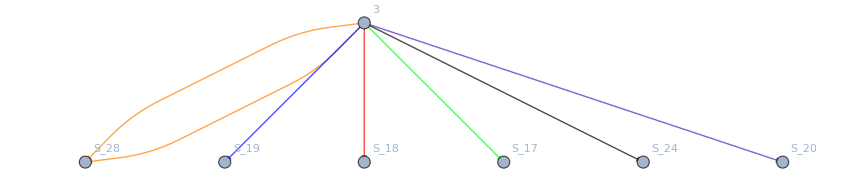

```mathematica
styles={Orange,Orange,Blue,Red,Green,Black,RGBColor[0.30382016, 0.13051672, 0.67703096]};
i=1;
Graph[{3->"S_28",3->"S_19",3->"S_18",3->"S_17",3->"S_24",3->"S_20",3->"S_28"},EdgeShapeFunction->({Arrowheads[Large],Thick,styles[[i++]],Arrow@#}&),VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

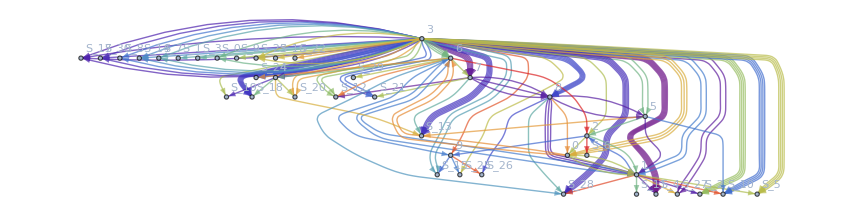

```mathematica
Graph[Flatten[end],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Automatic]
```

```mathematica
d=Import["C:\\Users\\DFCTech\\Desktop\\mogrid.csv"]
```

{{[ 3  1  6  9 25]},{[ 3  6  4 18]},{[ 3  4 20]},{[ 3  5  2  1 11]},{[ 3 17]},{[ 3 18]},{[3 7]},{[ 3 28]},{[ 3 13]},{[ 3  8  0  6 24]},{[ 3 23]},{[ 3 18]},{[3 2]},{[ 3  0  1 28]},{[3 4]},{[ 3  0  1 27]},{[ 3 17]},{[ 3 13]},{[ 3  8 28]},{[ 3  7 13]},{[3 0]},{[ 3 10]},{[ 3  5 13]},{[ 3 18]},{[ 3 28]},{[3 8]},{[3 2]},{[ 3 18]},{[3 2]},{[ 3 17]},{[ 3  8 26]},{[3 7]},{[ 3  7  8  5 10]},{[ 3 19]},{[3 2 0 1 5]},{[3 4]},{[3 3]},{[3 4]},{[ 3 14]},{[3 4]},{[3 0 6 2 6]},{[ 3 13]},{[ 3 28]},{[ 3 10]},{[3 4]},{[ 3 30]},{[3 5]},{[ 3  4 13]},{[ 3 10]},{[ 3  8  1 10]},{[ 3 24]},{[ 3 18]},{[ 3 24]},{[ 3 30]},{[ 3  9 26]},{[ 3 20]},{[ 3  7 12]},{[3 8]},{[ 3  6  7 21]},{[ 3 22]},{[ 3  1  6 28]},{[ 3 23]},{[ 3 28]},{[ 3 10]},{[ 3 28]},{[ 3 15]},{[ 3 12]},{[ 3  6 12]},{[ 3 17]},{[3 2]},{[ 3 21]},{[ 3 16]},{[ 3 13]},{[3 5]},{[3 4]},{[ 3 12]},{[ 3 13]},{[ 3 24]},{[3 0]},{[ 3  8  1  2  9 15]},{[ 3 14]},{[ 3  4 19]},{[ 3  6 29]},{[ 3 15]},{[3 5]},{[3 9]},{[ 3 27]},{[ 3 25]},{[ 3 27]},{[ 3 24]},{[ 3 14]},{[ 3 21]},{[3 7 8 1 2]},{[3 7 8 5 1 4]},{[ 3 20]},{[ 3 18]},{[3 5]},{[ 3 30]},{[ 3 23]},{[3 1]}}

```mathematica
Map[ToExpression,StringSplit[d⟦1⟧⟦1⟧]]
```

ToExpression::sntx: Invalid syntax in or before "[ ".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "25] ".
                                                    ^

{$Failed,3,1,6,9,$Failed}

```mathematica
d2="Episode: 0, Reward: -1207.79, avg loss: 0.000, eps: 0.998
Episode: 1, Reward: -1201.05, avg loss: 0.000, eps: 0.996
Episode: 2, Reward: -38.8, avg loss: 0.000, eps: 0.996
Episode: 3, Reward: -321.55999999999995, avg loss: 0.000, eps: 0.995
Episode: 4, Reward: -1201.0, avg loss: 0.000, eps: 0.994
Episode: 5, Reward: -0.82, avg loss: 0.000, eps: 0.994
Episode: 6, Reward: -3.03, avg loss: 0.000, eps: 0.993
Episode: 7, Reward: -479.76, avg loss: 0.000, eps: 0.992
Episode: 8, Reward: -168.03, avg loss: 0.000, eps: 0.988
Episode: 9, Reward: -49.1, avg loss: 0.000, eps: 0.986
Episode: 10, Reward: -186.05, avg loss: 0.000, eps: 0.985
Episode: 11, Reward: -1205.17, avg loss: 0.000, eps: 0.983
Episode: 12, Reward: -1201.0, avg loss: 0.000, eps: 0.982
Episode: 13, Reward: -1201.0, avg loss: 0.000, eps: 0.982
Episode: 14, Reward: -1201.0, avg loss: 0.000, eps: 0.981
Episode: 15, Reward: -1205.66, avg loss: 0.000, eps: 0.979
Episode: 16, Reward: -21.04, avg loss: 0.000, eps: 0.978
Episode: 17, Reward: -60.18, avg loss: 0.000, eps: 0.976
Episode: 18, Reward: -1201.0, avg loss: 0.000, eps: 0.975
Episode: 19, Reward: -433.49, avg loss: 0.000, eps: 0.974
Episode: 20, Reward: -1201.0, avg loss: 0.000, eps: 0.973
Episode: 21, Reward: -0.47, avg loss: 0.000, eps: 0.973
Episode: 22, Reward: -1204.67, avg loss: 0.000, eps: 0.971
Episode: 23, Reward: -1208.23, avg loss: 0.000, eps: 0.969
Episode: 24, Reward: -1202.99, avg loss: 0.000, eps: 0.968
Episode: 25, Reward: -64.78, avg loss: 0.000, eps: 0.967
Episode: 26, Reward: -1201.07, avg loss: 0.000, eps: 0.966
Episode: 27, Reward: 0.0, avg loss: 0.000, eps: 0.966
Episode: 28, Reward: -1201.0, avg loss: 0.000, eps: 0.965
Episode: 29, Reward: -59.879999999999995, avg loss: 0.000, eps: 0.965
Episode: 30, Reward: -102.94, avg loss: 0.000, eps: 0.964
Episode: 31, Reward: -1.18, avg loss: 0.000, eps: 0.964
Episode: 32, Reward: -1203.29, avg loss: 0.000, eps: 0.962
Episode: 33, Reward: -1201.0, avg loss: 0.000, eps: 0.961
Episode: 34, Reward: -10.43, avg loss: 0.000, eps: 0.960
Episode: 35, Reward: -0.14, avg loss: 0.000, eps: 0.959
Episode: 36, Reward: -646.26, avg loss: 0.000, eps: 0.959
Episode: 37, Reward: -5.73, avg loss: 0.000, eps: 0.958
Episode: 38, Reward: -1203.0, avg loss: 0.000, eps: 0.957
Episode: 39, Reward: -1204.35, avg loss: 0.000, eps: 0.955
Episode: 40, Reward: 1020.23, avg loss: 0.000, eps: 0.954
Episode: 41, Reward: -2.4699999999999998, avg loss: 3164045.906, eps: 0.952
Episode: 42, Reward: -1201.0, avg loss: 5093031.500, eps: 0.952
Episode: 43, Reward: -2.92, avg loss: 3961538.500, eps: 0.951
Episode: 44, Reward: -204.88, avg loss: 2895669.500, eps: 0.951
Episode: 45, Reward: -1201.0, avg loss: 3013328.000, eps: 0.950
Episode: 46, Reward: -1225.08, avg loss: 2101338.575, eps: 0.948
Episode: 47, Reward: -1205.29, avg loss: 2480868.902, eps: 0.947
Episode: 48, Reward: -1201.0, avg loss: 136614.016, eps: 0.946
Episode: 49, Reward: -1203.0, avg loss: 628590.418, eps: 0.945
Episode: 50, Reward: -1201.21, avg loss: 891913.312, eps: 0.944
Episode: 51, Reward: -1201.0, avg loss: 26464.510, eps: 0.944
Episode: 52, Reward: -1.17, avg loss: 571534.875, eps: 0.943
Episode: 53, Reward: -1201.0, avg loss: 2171353.250, eps: 0.943
Episode: 54, Reward: -1204.73, avg loss: 665961.056, eps: 0.941
Episode: 55, Reward: -1201.02, avg loss: 1980033.688, eps: 0.940
Episode: 56, Reward: -1203.01, avg loss: 1328988.547, eps: 0.939
Episode: 57, Reward: -1201.0, avg loss: 209907.797, eps: 0.939
Episode: 58, Reward: -1206.57, avg loss: 5361287.698, eps: 0.937
Episode: 59, Reward: -1208.93, avg loss: 6067416.266, eps: 0.935
Episode: 60, Reward: -1201.0, avg loss: 10308784.000, eps: 0.935
Episode: 61, Reward: -1201.0, avg loss: 2475319.500, eps: 0.934
Episode: 62, Reward: -1201.0, avg loss: 424549.125, eps: 0.934
Episode: 63, Reward: -2.02, avg loss: 600341.133, eps: 0.933
Episode: 64, Reward: -1202.4, avg loss: 774281.996, eps: 0.931
Episode: 65, Reward: -1202.05, avg loss: 1610698.906, eps: 0.930
Episode: 66, Reward: -1203.41, avg loss: 730773.500, eps: 0.929
Episode: 67, Reward: -231.62, avg loss: 1737549.562, eps: 0.928
Episode: 68, Reward: -1201.0, avg loss: 187155.406, eps: 0.928
Episode: 69, Reward: -1201.02, avg loss: 605151.938, eps: 0.927
Episode: 70, Reward: -1201.0, avg loss: 6288043.000, eps: 0.927
Episode: 71, Reward: -1201.0, avg loss: 598954.438, eps: 0.926
Episode: 72, Reward: -1203.12, avg loss: 2514419.781, eps: 0.925
Episode: 73, Reward: -91.45, avg loss: 836463.436, eps: 0.923
Episode: 74, Reward: -1203.0, avg loss: 2011174.688, eps: 0.922
Episode: 75, Reward: -134.69, avg loss: 3510850.250, eps: 0.922
Episode: 76, Reward: -1201.06, avg loss: 1772458.844, eps: 0.921
Episode: 77, Reward: -722.2, avg loss: 741115.500, eps: 0.920
Episode: 78, Reward: -1206.09, avg loss: 800147.385, eps: 0.918
Episode: 79, Reward: -9.629999999999999, avg loss: 297316.893, eps: 0.917
Episode: 80, Reward: -1221.01, avg loss: 78155.417, eps: 0.916
Episode: 81, Reward: -149.32, avg loss: 534395.875, eps: 0.915
Episode: 82, Reward: -28.990000000000002, avg loss: 385161.766, eps: 0.913
Episode: 83, Reward: -14.299999999999999, avg loss: 102012.914, eps: 0.911
Episode: 84, Reward: -156.49, avg loss: 62615.004, eps: 0.911
Episode: 85, Reward: -555.4, avg loss: 512195.692, eps: 0.908
Episode: 86, Reward: -1201.0, avg loss: 45034.664, eps: 0.907
Episode: 87, Reward: -1201.0, avg loss: 19840.023, eps: 0.907
Episode: 88, Reward: -904.6999999999999, avg loss: 92753.022, eps: 0.905
Episode: 89, Reward: -1201.01, avg loss: 61230.763, eps: 0.904
Episode: 90, Reward: -1201.03, avg loss: 395115.609, eps: 0.904
Episode: 91, Reward: -1201.0, avg loss: 40808.906, eps: 0.903
Episode: 92, Reward: -2.2099999999999995, avg loss: 518178.214, eps: 0.902
Episode: 93, Reward: -1201.0, avg loss: 7137.926, eps: 0.901
Episode: 94, Reward: -1203.77, avg loss: 33588.871, eps: 0.899
Episode: 95, Reward: -1201.0, avg loss: 58501.805, eps: 0.899
Episode: 96, Reward: -1201.0, avg loss: 6828.011, eps: 0.898
Episode: 97, Reward: -1203.11, avg loss: 15059.494, eps: 0.897
Episode: 98, Reward: -9.86, avg loss: 61373.432, eps: 0.896
Episode: 99, Reward: -556.5, avg loss: 5969.927, eps: 0.896
Episode: 100, Reward: -514.9799999999999, avg loss: 87724.531, eps: 0.895
Episode: 101, Reward: -1203.06, avg loss: 54390.069, eps: 0.893
Episode: 102, Reward: -2.56, avg loss: 57680.813, eps: 0.892
Episode: 103, Reward: -1.17, avg loss: 5597.340, eps: 0.892
Episode: 104, Reward: -16.36, avg loss: 47828.843, eps: 0.890
Episode: 105, Reward: -54.33, avg loss: 74458.039, eps: 0.890
Episode: 106, Reward: -1201.0, avg loss: 156951.395, eps: 0.889
Episode: 107, Reward: -0.46, avg loss: 11169.210, eps: 0.887
Episode: 108, Reward: -127.38000000000001, avg loss: 54150.696, eps: 0.885
Episode: 109, Reward: -94.05, avg loss: 626403.458, eps: 0.881
Episode: 110, Reward: -21.44, avg loss: 10292.823, eps: 0.880
Episode: 111, Reward: -1201.14, avg loss: 68979.176, eps: 0.879
Episode: 112, Reward: -1201.0, avg loss: 81001.031, eps: 0.879
Episode: 113, Reward: -1201.0, avg loss: 56247.613, eps: 0.878
Episode: 114, Reward: -1201.0, avg loss: 1772458.938, eps: 0.878
Episode: 115, Reward: -1225.12, avg loss: 1059601.955, eps: 0.876
Episode: 116, Reward: -6.99, avg loss: 44625.523, eps: 0.875
Episode: 117, Reward: -1.22, avg loss: 25959.596, eps: 0.874
Episode: 118, Reward: -686.36, avg loss: 1032108.438, eps: 0.874
Episode: 119, Reward: -0.07, avg loss: 302099.270, eps: 0.872
Episode: 120, Reward: -1221.01, avg loss: 713379.824, eps: 0.872
Episode: 121, Reward: -1201.0, avg loss: 238921.578, eps: 0.871
Episode: 122, Reward: 0.0, avg loss: 458503.219, eps: 0.871
Episode: 123, Reward: 497.63, avg loss: 173991.465, eps: 0.870
Episode: 124, Reward: -1201.0, avg loss: 1252839.000, eps: 0.869
Episode: 125, Reward: -1201.0, avg loss: 243885.250, eps: 0.869
Episode: 126, Reward: -18.06, avg loss: 358387.626, eps: 0.864
Episode: 127, Reward: -1201.0, avg loss: 34252.680, eps: 0.864
Episode: 128, Reward: -1201.0, avg loss: 18512.643, eps: 0.863
Episode: 129, Reward: -23.630000000000003, avg loss: 55780.556, eps: 0.862
Episode: 130, Reward: -1202.99, avg loss: 683315.133, eps: 0.861
Episode: 131, Reward: -1207.41, avg loss: 334458.743, eps: 0.857
Episode: 132, Reward: -1201.0, avg loss: 17921.578, eps: 0.857
Episode: 133, Reward: -212.6, avg loss: 83334.572, eps: 0.856
Episode: 134, Reward: -20.38, avg loss: 740272.750, eps: 0.854
Episode: 135, Reward: -1201.0, avg loss: 130945.016, eps: 0.854
Episode: 136, Reward: -1201.0, avg loss: 24472.744, eps: 0.853
Episode: 137, Reward: -1201.0, avg loss: 52804.938, eps: 0.853
Episode: 138, Reward: -1201.0, avg loss: 77087.562, eps: 0.852
Episode: 139, Reward: -1203.02, avg loss: 92466.022, eps: 0.851
Episode: 140, Reward: -1201.67, avg loss: 146852.715, eps: 0.850
Episode: 141, Reward: -1201.0, avg loss: 77924.789, eps: 0.850
Episode: 142, Reward: -1201.0, avg loss: 16173.939, eps: 0.849
Episode: 143, Reward: -1203.0, avg loss: 53786.209, eps: 0.849
Episode: 144, Reward: -1212.48, avg loss: 381430.219, eps: 0.847
Episode: 145, Reward: -1201.0, avg loss: 1594390.250, eps: 0.847
Episode: 146, Reward: -0.9400000000000001, avg loss: 168190.766, eps: 0.846
Episode: 147, Reward: -124.24, avg loss: 52835.978, eps: 0.845
Episode: 148, Reward: -1223.02, avg loss: 137788.204, eps: 0.844
Episode: 149, Reward: -1201.0, avg loss: 112199.875, eps: 0.844
Episode: 150, Reward: -156.34, avg loss: 587680.818, eps: 0.843
Episode: 151, Reward: -25.4, avg loss: 206961.510, eps: 0.841
Episode: 152, Reward: -146.37, avg loss: 1240442.250, eps: 0.841
Episode: 153, Reward: -1201.0, avg loss: 51891.324, eps: 0.841
Episode: 154, Reward: -1201.0, avg loss: 4257.667, eps: 0.840
Episode: 155, Reward: -166.89, avg loss: 130140.391, eps: 0.840
Episode: 156, Reward: -19.89, avg loss: 212058.594, eps: 0.839
Episode: 157, Reward: -1205.11, avg loss: 187190.667, eps: 0.838
Episode: 158, Reward: -1203.24, avg loss: 104527.656, eps: 0.837
Episode: 159, Reward: -613.07, avg loss: 211674.234, eps: 0.837
Episode: 160, Reward: -1201.72, avg loss: 248921.234, eps: 0.836
Episode: 161, Reward: -21.030000000000005, avg loss: 169979.445, eps: 0.834
Episode: 162, Reward: -214.89, avg loss: 92515.672, eps: 0.834
Episode: 163, Reward: -592.15, avg loss: 227437.646, eps: 0.832
Episode: 164, Reward: -1205.08, avg loss: 172832.746, eps: 0.831
Episode: 165, Reward: -1.19, avg loss: 315993.984, eps: 0.830
Episode: 166, Reward: -21.31, avg loss: 69819.469, eps: 0.830
Episode: 167, Reward: -1231.74, avg loss: 222646.273, eps: 0.826
Episode: 168, Reward: 0.0, avg loss: 52488.785, eps: 0.826
Episode: 169, Reward: -1201.0, avg loss: 67058.844, eps: 0.825
Episode: 170, Reward: -1201.0, avg loss: 100056.305, eps: 0.825
Episode: 171, Reward: -0.02, avg loss: 97660.102, eps: 0.825
Episode: 172, Reward: -409.03, avg loss: 198521.568, eps: 0.823
Episode: 173, Reward: -8.379999999999999, avg loss: 360822.719, eps: 0.822
Episode: 174, Reward: -28.63, avg loss: 1511781.045, eps: 0.821
Episode: 175, Reward: -1201.0, avg loss: 76310.719, eps: 0.820
Episode: 176, Reward: -1201.12, avg loss: 34272.376, eps: 0.819
Episode: 177, Reward: -1201.0, avg loss: 183266.715, eps: 0.819
Episode: 178, Reward: -269.78000000000003, avg loss: 266697.497, eps: 0.817
Episode: 179, Reward: -1201.0, avg loss: 307738.594, eps: 0.817
Episode: 180, Reward: -516.61, avg loss: 360294.344, eps: 0.817
Episode: 181, Reward: -44.010000000000005, avg loss: 912032.062, eps: 0.815
Episode: 182, Reward: -1201.01, avg loss: 186374.934, eps: 0.814
Episode: 183, Reward: -12.23, avg loss: 240188.094, eps: 0.814
Episode: 184, Reward: -1205.02, avg loss: 221639.240, eps: 0.812
Episode: 185, Reward: -1201.0, avg loss: 1757137.750, eps: 0.812
Episode: 186, Reward: -475.78, avg loss: 208554.893, eps: 0.811
Episode: 187, Reward: -1201.0, avg loss: 278865.312, eps: 0.810
Episode: 188, Reward: -278.44, avg loss: 489958.878, eps: 0.808
Episode: 189, Reward: -1201.0, avg loss: 582453.125, eps: 0.808
Episode: 190, Reward: -163.15, avg loss: 225351.219, eps: 0.808
Episode: 191, Reward: -1201.0, avg loss: 431717.375, eps: 0.807
Episode: 192, Reward: -1201.0, avg loss: 156317.828, eps: 0.807
Episode: 193, Reward: -1201.02, avg loss: 336513.812, eps: 0.806
Episode: 194, Reward: -1.73, avg loss: 176823.277, eps: 0.804
Episode: 195, Reward: -1205.45, avg loss: 238951.891, eps: 0.803
Episode: 196, Reward: -1201.0, avg loss: 39070.758, eps: 0.803
Episode: 197, Reward: -1203.63, avg loss: 679532.844, eps: 0.802
Episode: 198, Reward: -103.19, avg loss: 359981.531, eps: 0.801
Episode: 199, Reward: -1203.12, avg loss: 192390.289, eps: 0.800
Episode: 200, Reward: -85.03, avg loss: 653207.375, eps: 0.799
Episode: 201, Reward: -217.34, avg loss: 672993.000, eps: 0.799
Episode: 202, Reward: -1.67, avg loss: 255719.203, eps: 0.799
Episode: 203, Reward: -2.85, avg loss: 216663.628, eps: 0.797
Episode: 204, Reward: -1.22, avg loss: 191995.175, eps: 0.795
Episode: 205, Reward: -1204.16, avg loss: 135128.183, eps: 0.793
Episode: 206, Reward: -1207.16, avg loss: 173108.038, eps: 0.791
Episode: 207, Reward: -51.9, avg loss: 116149.637, eps: 0.790
Episode: 208, Reward: -1201.0, avg loss: 198728.172, eps: 0.790
Episode: 209, Reward: -1201.0, avg loss: 141241.312, eps: 0.790
Episode: 210, Reward: -1205.42, avg loss: 91952.284, eps: 0.788
Episode: 211, Reward: -8.45, avg loss: 249960.828, eps: 0.788
Episode: 212, Reward: -1205.13, avg loss: 157373.302, eps: 0.786
Episode: 213, Reward: -54.57, avg loss: 85457.266, eps: 0.785
Episode: 214, Reward: -1237.8, avg loss: 273488.812, eps: 0.784
Episode: 215, Reward: -0.11, avg loss: 147095.359, eps: 0.784
Episode: 216, Reward: -1203.98, avg loss: 103541.941, eps: 0.783
Episode: 217, Reward: -38.89, avg loss: 149503.375, eps: 0.783
Episode: 218, Reward: -2.3200000000000003, avg loss: 105867.371, eps: 0.782
Episode: 219, Reward: -1203.0, avg loss: 133779.812, eps: 0.781
Episode: 220, Reward: -1203.1, avg loss: 56487.365, eps: 0.780
Episode: 221, Reward: -11.299999999999999, avg loss: 54524.523, eps: 0.778
Episode: 222, Reward: -1203.06, avg loss: 33320.874, eps: 0.776
Episode: 223, Reward: -1201.0, avg loss: 35449.414, eps: 0.776
Episode: 224, Reward: -1250.38, avg loss: 25051.005, eps: 0.775
Episode: 225, Reward: -1201.0, avg loss: 15290.412, eps: 0.774
Episode: 226, Reward: -199.98, avg loss: 15148.880, eps: 0.774
Episode: 227, Reward: -1222.12, avg loss: 40836.395, eps: 0.773
Episode: 228, Reward: -1201.0, avg loss: 56104.703, eps: 0.772
Episode: 229, Reward: -7.76, avg loss: 55233.063, eps: 0.770
Episode: 230, Reward: -1.57, avg loss: 20673.329, eps: 0.769
Episode: 231, Reward: -1207.25, avg loss: 44393.881, eps: 0.766
Episode: 232, Reward: -6.92, avg loss: 28021.719, eps: 0.766
Episode: 233, Reward: -1201.0, avg loss: 20383.459, eps: 0.765
Episode: 234, Reward: -1205.54, avg loss: 25135.245, eps: 0.764
Episode: 235, Reward: -1201.0, avg loss: 33261.941, eps: 0.764
Episode: 236, Reward: -1207.34, avg loss: 46838.340, eps: 0.762
Episode: 237, Reward: -1201.0, avg loss: 44684.070, eps: 0.762
Episode: 238, Reward: -17.22, avg loss: 25780.023, eps: 0.761
Episode: 239, Reward: -31.61, avg loss: 35528.116, eps: 0.759
Episode: 240, Reward: -1203.08, avg loss: 27001.918, eps: 0.759
Episode: 241, Reward: -1201.1, avg loss: 48808.163, eps: 0.757
Episode: 242, Reward: -350.58, avg loss: 17293.348, eps: 0.757
Episode: 243, Reward: -0.32, avg loss: 9764.886, eps: 0.756
Episode: 244, Reward: -1203.52, avg loss: 18247.129, eps: 0.755
Episode: 245, Reward: -1209.6, avg loss: 16279.418, eps: 0.752
Episode: 246, Reward: -1227.09, avg loss: 23396.000, eps: 0.750
Episode: 247, Reward: -1201.0, avg loss: 37426.191, eps: 0.750
Episode: 248, Reward: -1201.0, avg loss: 29404.584, eps: 0.750
Episode: 249, Reward: 0.0, avg loss: 81371.625, eps: 0.749
Episode: 250, Reward: -1225.71, avg loss: 42538.358, eps: 0.747
Episode: 251, Reward: -84.82, avg loss: 20743.096, eps: 0.746
Episode: 252, Reward: -1201.0, avg loss: 23731.834, eps: 0.745
Episode: 253, Reward: -1201.0, avg loss: 56514.133, eps: 0.745
Episode: 254, Reward: -148.82, avg loss: 9326.475, eps: 0.744
Episode: 255, Reward: -1203.16, avg loss: 27311.612, eps: 0.742
Episode: 256, Reward: -1205.28, avg loss: 17756.985, eps: 0.739
Episode: 257, Reward: -333.96, avg loss: 28706.762, eps: 0.738
Episode: 258, Reward: -1205.43, avg loss: 25295.959, eps: 0.735
Episode: 259, Reward: -139.22, avg loss: 19261.469, eps: 0.734
Episode: 260, Reward: -1201.0, avg loss: 28004.465, eps: 0.734
Episode: 261, Reward: -1206.79, avg loss: 23934.880, eps: 0.731
Episode: 262, Reward: -37.08, avg loss: 8099.232, eps: 0.731
Episode: 263, Reward: -162.73, avg loss: 25512.124, eps: 0.730
Episode: 264, Reward: -960.32, avg loss: 22221.729, eps: 0.729
Episode: 265, Reward: -1205.2, avg loss: 28225.396, eps: 0.728
Episode: 266, Reward: -1201.43, avg loss: 21577.011, eps: 0.727
Episode: 267, Reward: -26.42, avg loss: 22671.720, eps: 0.727
Episode: 268, Reward: -1203.22, avg loss: 20834.465, eps: 0.725
Episode: 269, Reward: -3.0999999999999996, avg loss: 25966.695, eps: 0.724
Episode: 270, Reward: -0.05, avg loss: 15053.173, eps: 0.723
Episode: 271, Reward: -1202.24, avg loss: 18571.036, eps: 0.721
Episode: 272, Reward: -96.69, avg loss: 21965.878, eps: 0.720
Episode: 273, Reward: -23.770000000000003, avg loss: 14242.237, eps: 0.720
Episode: 274, Reward: -575.16, avg loss: 8948.042, eps: 0.717
Episode: 275, Reward: -1206.88, avg loss: 19330.389, eps: 0.716
Episode: 276, Reward: -23.4, avg loss: 7045.778, eps: 0.716
Episode: 277, Reward: -93.63999999999999, avg loss: 20220.828, eps: 0.715
Episode: 278, Reward: -1201.0, avg loss: 8054.649, eps: 0.715
Episode: 279, Reward: -1230.92, avg loss: 143189.635, eps: 0.711
Episode: 280, Reward: -1201.0, avg loss: 39531.207, eps: 0.711
Episode: 281, Reward: -1222.8, avg loss: 71408.563, eps: 0.709
Episode: 282, Reward: -199.14, avg loss: 23664.430, eps: 0.709
Episode: 283, Reward: -1201.0, avg loss: 41777.828, eps: 0.709
Episode: 284, Reward: -1201.0, avg loss: 20554.691, eps: 0.708
Episode: 285, Reward: -1201.27, avg loss: 12211.424, eps: 0.708
Episode: 286, Reward: -1203.0, avg loss: 43080.383, eps: 0.707
Episode: 287, Reward: -1201.0, avg loss: 43232.059, eps: 0.707
Episode: 288, Reward: -1201.0, avg loss: 203598.562, eps: 0.706
Episode: 289, Reward: -1201.0, avg loss: 30051.375, eps: 0.706
Episode: 290, Reward: -6.22, avg loss: 9619.436, eps: 0.705
Episode: 291, Reward: -2.84, avg loss: 21357.461, eps: 0.705
Episode: 292, Reward: -1258.11, avg loss: 23623.792, eps: 0.704
Episode: 293, Reward: -2.45, avg loss: 50236.655, eps: 0.703
Episode: 294, Reward: -129.09, avg loss: 90157.758, eps: 0.702
Episode: 295, Reward: -1201.0, avg loss: 12161.247, eps: 0.701
Episode: 296, Reward: -5.719999999999999, avg loss: 24489.141, eps: 0.700
Episode: 297, Reward: -0.08, avg loss: 10609.198, eps: 0.700
Episode: 298, Reward: -1203.18, avg loss: 31265.696, eps: 0.699
Episode: 299, Reward: -1203.23, avg loss: 16428.343, eps: 0.698
Episode: 300, Reward: -35.68, avg loss: 6805.415, eps: 0.698
Episode: 301, Reward: -1203.0, avg loss: 61800.229, eps: 0.697
Episode: 302, Reward: -46.33, avg loss: 22690.985, eps: 0.697
Episode: 303, Reward: -1201.0, avg loss: 5510.446, eps: 0.696
Episode: 304, Reward: -1205.0, avg loss: 40116.760, eps: 0.695
Episode: 305, Reward: -94.91, avg loss: 3933.171, eps: 0.695
Episode: 306, Reward: -1203.0, avg loss: 46136.353, eps: 0.693
Episode: 307, Reward: -1201.0, avg loss: 21660.760, eps: 0.693
Episode: 308, Reward: -1204.35, avg loss: 11459.379, eps: 0.692
Episode: 309, Reward: -115.86999999999999, avg loss: 22463.533, eps: 0.691
Episode: 310, Reward: -1201.01, avg loss: 132946.639, eps: 0.691
Episode: 311, Reward: -1201.0, avg loss: 70593.695, eps: 0.690
Episode: 312, Reward: -425.37, avg loss: 21303.527, eps: 0.688
Episode: 313, Reward: -1203.24, avg loss: 16270.430, eps: 0.686
Episode: 314, Reward: -397.06, avg loss: 18536.000, eps: 0.685
Episode: 315, Reward: -268.16, avg loss: 31832.886, eps: 0.684
Episode: 316, Reward: -1205.24, avg loss: 25896.928, eps: 0.682
Episode: 317, Reward: -4.66, avg loss: 183563.958, eps: 0.681
Episode: 318, Reward: -34.3, avg loss: 13145.201, eps: 0.681
Episode: 319, Reward: -177.02, avg loss: 51547.954, eps: 0.679
Episode: 320, Reward: -838.83, avg loss: 35012.523, eps: 0.679
Episode: 321, Reward: -578.04, avg loss: 55776.508, eps: 0.678
Episode: 322, Reward: -1201.0, avg loss: 13607.490, eps: 0.678
Episode: 323, Reward: -1.04, avg loss: 14729.348, eps: 0.677
Episode: 324, Reward: 0.0, avg loss: 22038.266, eps: 0.677
Episode: 325, Reward: -41.269999999999996, avg loss: 174871.583, eps: 0.675
Episode: 326, Reward: -0.01, avg loss: 267275.156, eps: 0.674
Episode: 327, Reward: -17.0, avg loss: 498338.449, eps: 0.673
Episode: 328, Reward: -1201.0, avg loss: 27935.678, eps: 0.672
Episode: 329, Reward: -1201.0, avg loss: 123849.828, eps: 0.672
Episode: 330, Reward: -63.93, avg loss: 101480.937, eps: 0.670
Episode: 331, Reward: -69.82, avg loss: 12622.945, eps: 0.670
Episode: 332, Reward: -10.27, avg loss: 279633.344, eps: 0.670
Episode: 333, Reward: -1203.01, avg loss: 156952.677, eps: 0.669
Episode: 334, Reward: -666.47, avg loss: 9392.973, eps: 0.668
Episode: 335, Reward: -1204.9, avg loss: 735990.068, eps: 0.666
Episode: 336, Reward: -1201.0, avg loss: 588022.562, eps: 0.666
Episode: 337, Reward: -1205.17, avg loss: 67358.261, eps: 0.664
Episode: 338, Reward: -689.9399999999999, avg loss: 115344.609, eps: 0.663
Episode: 339, Reward: -633.31, avg loss: 186687.578, eps: 0.663
Episode: 340, Reward: -1203.04, avg loss: 188576.515, eps: 0.662
Episode: 341, Reward: -1201.04, avg loss: 56146.079, eps: 0.661
Episode: 342, Reward: -17.77, avg loss: 5929.796, eps: 0.661
Episode: 343, Reward: -79.57000000000001, avg loss: 32671.660, eps: 0.660
Episode: 344, Reward: -48.35, avg loss: 621519.750, eps: 0.660
Episode: 345, Reward: -577.13, avg loss: 45399.383, eps: 0.660
Episode: 346, Reward: -1202.32, avg loss: 73067.148, eps: 0.659
Episode: 347, Reward: -54.54, avg loss: 89975.367, eps: 0.658
Episode: 348, Reward: -1201.0, avg loss: 34434.707, eps: 0.658
Episode: 349, Reward: -895.75, avg loss: 166743.455, eps: 0.655
Episode: 350, Reward: -1201.0, avg loss: 10896.129, eps: 0.655
Episode: 351, Reward: -1203.0, avg loss: 6151.786, eps: 0.654
Episode: 352, Reward: -14.67, avg loss: 146081.298, eps: 0.653
Episode: 353, Reward: -1201.0, avg loss: 29954.123, eps: 0.653
Episode: 354, Reward: -1206.39, avg loss: 211624.865, eps: 0.652
Episode: 355, Reward: -1205.15, avg loss: 409701.812, eps: 0.650
Episode: 356, Reward: -5.18, avg loss: 31966.963, eps: 0.650
Episode: 357, Reward: -231.08999999999997, avg loss: 23466.557, eps: 0.649
Episode: 358, Reward: -1201.0, avg loss: 243132.453, eps: 0.649
Episode: 359, Reward: -1203.01, avg loss: 82472.947, eps: 0.648
Episode: 360, Reward: -1204.47, avg loss: 68761.135, eps: 0.647
Episode: 361, Reward: -76.14, avg loss: 44833.210, eps: 0.644
Episode: 362, Reward: -1201.0, avg loss: 90488.328, eps: 0.644
Episode: 363, Reward: -1201.0, avg loss: 11592.558, eps: 0.643
Episode: 364, Reward: -232.07, avg loss: 975686.938, eps: 0.643
Episode: 365, Reward: -1215.18, avg loss: 41819.188, eps: 0.643
Episode: 366, Reward: -1197.8, avg loss: 3348646.389, eps: 0.642
Episode: 367, Reward: -1201.03, avg loss: 835408.203, eps: 0.641
Episode: 368, Reward: -6.020000000000001, avg loss: 4295452.552, eps: 0.639
Episode: 369, Reward: -1207.55, avg loss: 513050.808, eps: 0.638
Episode: 370, Reward: -21.23, avg loss: 7939301.758, eps: 0.637
Episode: 371, Reward: -1218.14, avg loss: 915314.695, eps: 0.635
Episode: 372, Reward: -45.400000000000006, avg loss: 3568420.896, eps: 0.634
Episode: 373, Reward: -196.82, avg loss: 7983178.331, eps: 0.631
Episode: 374, Reward: -58.650000000000006, avg loss: 806151.750, eps: 0.631
Episode: 375, Reward: -1206.18, avg loss: 12737122.673, eps: 0.629
Episode: 376, Reward: -46.06, avg loss: 36719064.023, eps: 0.628
Episode: 377, Reward: -2.27, avg loss: 397203.094, eps: 0.627
Episode: 378, Reward: -18.02, avg loss: 23204401.750, eps: 0.626
Episode: 379, Reward: -7.78, avg loss: 12179525.412, eps: 0.625
Episode: 380, Reward: -102.66, avg loss: 24280683.853, eps: 0.624
Episode: 381, Reward: -50.22, avg loss: 16518822.917, eps: 0.623
Episode: 382, Reward: -1201.0, avg loss: 29039356.000, eps: 0.622
Episode: 383, Reward: -69.06, avg loss: 43153868.000, eps: 0.622
Episode: 384, Reward: -1203.0, avg loss: 84944161.625, eps: 0.621
Episode: 385, Reward: -205.39, avg loss: 28703.604, eps: 0.621
Episode: 386, Reward: -50.38, avg loss: 1094037.281, eps: 0.620
Episode: 387, Reward: -1263.69, avg loss: 65851609.019, eps: 0.617
Episode: 388, Reward: -116.2, avg loss: 20897086.000, eps: 0.617
Episode: 389, Reward: -237.23, avg loss: 15977519.000, eps: 0.617
Episode: 390, Reward: -1227.91, avg loss: 37987589.076, eps: 0.615
Episode: 391, Reward: -5.6899999999999995, avg loss: 20281059.538, eps: 0.613
Episode: 392, Reward: -708.34, avg loss: 5077237.477, eps: 0.613
Episode: 393, Reward: -1220.81, avg loss: 72120068.237, eps: 0.611
Episode: 394, Reward: -530.03, avg loss: 614815.562, eps: 0.611
Episode: 395, Reward: -1201.23, avg loss: 1288011.079, eps: 0.610
Episode: 396, Reward: -1201.0, avg loss: 2272332.250, eps: 0.609
Episode: 397, Reward: -1205.01, avg loss: 15706462.250, eps: 0.608
Episode: 398, Reward: -9.24, avg loss: 17478273.625, eps: 0.607
Episode: 399, Reward: -1201.09, avg loss: 26269512.000, eps: 0.607
Episode: 400, Reward: -61.93, avg loss: 7024875.312, eps: 0.606
Episode: 401, Reward: -1.26, avg loss: 12124157.103, eps: 0.605
Episode: 402, Reward: -1201.0, avg loss: 1208941.844, eps: 0.605
Episode: 403, Reward: -104.53999999999999, avg loss: 3422625.732, eps: 0.603
Episode: 404, Reward: -1205.15, avg loss: 7527369.812, eps: 0.602
Episode: 405, Reward: -1203.01, avg loss: 6070708.488, eps: 0.601
Episode: 406, Reward: -1201.67, avg loss: 4642600.445, eps: 0.600
Episode: 407, Reward: -722.67, avg loss: 439069.734, eps: 0.599
Episode: 408, Reward: -1203.07, avg loss: 843834.878, eps: 0.598
Episode: 409, Reward: -7.029999999999999, avg loss: 1672314.292, eps: 0.597
Episode: 410, Reward: -4.78, avg loss: 776991.711, eps: 0.596
Episode: 411, Reward: -60.080000000000005, avg loss: 2902338.630, eps: 0.595
Episode: 412, Reward: -1201.0, avg loss: 483438.750, eps: 0.594
Episode: 413, Reward: -1201.0, avg loss: 190453.687, eps: 0.594
Episode: 414, Reward: -1216.85, avg loss: 1122465.383, eps: 0.592
Episode: 415, Reward: -3.25, avg loss: 3762866.603, eps: 0.592
Episode: 416, Reward: -1201.0, avg loss: 1323787.344, eps: 0.591
Episode: 417, Reward: -14.0, avg loss: 2854538.068, eps: 0.591
Episode: 418, Reward: -33.129999999999995, avg loss: 2672956.576, eps: 0.589
Episode: 419, Reward: -17.53, avg loss: 722097.375, eps: 0.589
Episode: 420, Reward: -1201.0, avg loss: 4169535.250, eps: 0.588
Episode: 421, Reward: -1201.0, avg loss: 3741747.000, eps: 0.588
Episode: 422, Reward: -1205.49, avg loss: 12597583.868, eps: 0.586
Episode: 423, Reward: -1203.25, avg loss: 2074798.108, eps: 0.585
Episode: 424, Reward: -1205.79, avg loss: 3317137.719, eps: 0.583
Episode: 425, Reward: -9.77, avg loss: 1096093.480, eps: 0.582
Episode: 426, Reward: -13.76, avg loss: 1405435.156, eps: 0.582
Episode: 427, Reward: -0.81, avg loss: 233769.797, eps: 0.581
Episode: 428, Reward: -269.12, avg loss: 1904404.997, eps: 0.580
Episode: 429, Reward: -252.23, avg loss: 458603.625, eps: 0.580
Episode: 430, Reward: -1229.42, avg loss: 4347098.165, eps: 0.577
Episode: 431, Reward: -93.99, avg loss: 429831.051, eps: 0.575
Episode: 432, Reward: -0.2, avg loss: 299453.411, eps: 0.574
Episode: 433, Reward: -8.299999999999999, avg loss: 1626959.244, eps: 0.574
Episode: 434, Reward: -1205.42, avg loss: 467163.229, eps: 0.573
Episode: 435, Reward: -6.2299999999999995, avg loss: 1453499.887, eps: 0.571
Episode: 436, Reward: -5.4, avg loss: 695642.125, eps: 0.571
Episode: 437, Reward: -5.74, avg loss: 120381.766, eps: 0.570
Episode: 438, Reward: -1201.02, avg loss: 1260096.125, eps: 0.570
Episode: 439, Reward: -1201.0, avg loss: 468363.219, eps: 0.569
Episode: 440, Reward: -35.75, avg loss: 865782.174, eps: 0.568
Episode: 441, Reward: -1.83, avg loss: 65032.000, eps: 0.568
Episode: 442, Reward: -1210.1, avg loss: 266513.045, eps: 0.567
Episode: 443, Reward: -1210.09, avg loss: 1218153.019, eps: 0.564
Episode: 444, Reward: -1205.39, avg loss: 1087667.510, eps: 0.562
Episode: 445, Reward: -6.22, avg loss: 329614.301, eps: 0.562
Episode: 446, Reward: -1.51, avg loss: 68046.703, eps: 0.561
Episode: 447, Reward: 328.3, avg loss: 1355073.656, eps: 0.561
Episode: 448, Reward: -8.26, avg loss: 367957.617, eps: 0.560
Episode: 449, Reward: -1203.02, avg loss: 978725.969, eps: 0.560
Episode: 450, Reward: -1201.0, avg loss: 817493.250, eps: 0.559
Episode: 451, Reward: -1207.05, avg loss: 4498295.452, eps: 0.558
Episode: 452, Reward: -1207.15, avg loss: 817754.124, eps: 0.556
Episode: 453, Reward: -1203.0, avg loss: 215757.865, eps: 0.555
Episode: 454, Reward: -1203.0, avg loss: 1353239.875, eps: 0.554
Episode: 455, Reward: -37.96, avg loss: 1151190.594, eps: 0.553
Episode: 456, Reward: -1201.0, avg loss: 288928.417, eps: 0.553
Episode: 457, Reward: -1203.0, avg loss: 586691.031, eps: 0.552
Episode: 458, Reward: -1201.0, avg loss: 313423.281, eps: 0.552
Episode: 459, Reward: -1227.83, avg loss: 414567.705, eps: 0.550
Episode: 460, Reward: -109.21, avg loss: 2020753.965, eps: 0.548
Episode: 461, Reward: -1201.0, avg loss: 301012.281, eps: 0.548
Episode: 462, Reward: -14.59, avg loss: 925900.188, eps: 0.547
Episode: 463, Reward: -1201.0, avg loss: 298393.312, eps: 0.547
Episode: 464, Reward: -1201.0, avg loss: 6299.270, eps: 0.547
Episode: 465, Reward: -9.069999999999999, avg loss: 697636.262, eps: 0.544
Episode: 466, Reward: -1207.31, avg loss: 739047.787, eps: 0.543
Episode: 467, Reward: -10.85, avg loss: 224875.078, eps: 0.543
Episode: 468, Reward: -35.910000000000004, avg loss: 363596.641, eps: 0.541
Episode: 469, Reward: -1201.0, avg loss: 171112.594, eps: 0.541
Episode: 470, Reward: -1230.01, avg loss: 335353.859, eps: 0.538
Episode: 471, Reward: -1201.0, avg loss: 64255.105, eps: 0.538
Episode: 472, Reward: -79.84, avg loss: 483574.844, eps: 0.537
Episode: 473, Reward: -117.97, avg loss: 404982.229, eps: 0.536
Episode: 474, Reward: -1201.0, avg loss: 672685.375, eps: 0.536
Episode: 475, Reward: -1203.74, avg loss: 110969.781, eps: 0.536
Episode: 476, Reward: -238.89000000000001, avg loss: 538047.895, eps: 0.534
Episode: 477, Reward: -14.94, avg loss: 421736.125, eps: 0.534
Episode: 478, Reward: -1209.53, avg loss: 188440.125, eps: 0.531
Episode: 479, Reward: -1201.0, avg loss: 10376.379, eps: 0.531
Episode: 480, Reward: -34.71, avg loss: 562533.312, eps: 0.531
Episode: 481, Reward: -1215.77, avg loss: 270135.565, eps: 0.528
Episode: 482, Reward: -1201.0, avg loss: 161837.891, eps: 0.528
Episode: 483, Reward: -1201.0, avg loss: 10094.676, eps: 0.528
Episode: 484, Reward: -1203.24, avg loss: 1116775.984, eps: 0.527
Episode: 485, Reward: -1203.0, avg loss: 88777.471, eps: 0.526
Episode: 486, Reward: -186.60999999999999, avg loss: 273102.681, eps: 0.525
Episode: 487, Reward: -1203.0, avg loss: 75953.958, eps: 0.524
Episode: 488, Reward: -1201.0, avg loss: 118877.281, eps: 0.524
Episode: 489, Reward: -1171.3, avg loss: 57513.292, eps: 0.523
Episode: 490, Reward: -622.5200000000001, avg loss: 249918.058, eps: 0.521
Episode: 491, Reward: -62.44, avg loss: 586293.740, eps: 0.519
Episode: 492, Reward: -1203.0, avg loss: 341268.227, eps: 0.518
Episode: 493, Reward: -1203.0, avg loss: 127018.862, eps: 0.518
Episode: 494, Reward: -320.21, avg loss: 33881.691, eps: 0.517
Episode: 495, Reward: -1217.37, avg loss: 145887.663, eps: 0.515
Episode: 496, Reward: -1202.07, avg loss: 88345.066, eps: 0.514
Episode: 497, Reward: -24.68, avg loss: 266126.250, eps: 0.513
Episode: 498, Reward: -309.26, avg loss: 222070.372, eps: 0.512
Episode: 499, Reward: -1206.17, avg loss: 267217.475, eps: 0.509
Episode: 500, Reward: -2.07, avg loss: 210527.312, eps: 0.509
Episode: 501, Reward: -15.05, avg loss: 35648.426, eps: 0.509
Episode: 502, Reward: -1229.58, avg loss: 368506.019, eps: 0.506
Episode: 503, Reward: -59.74, avg loss: 420084.044, eps: 0.505
Episode: 504, Reward: -1203.0, avg loss: 188649.940, eps: 0.505
Episode: 505, Reward: -1205.82, avg loss: 276224.357, eps: 0.503
Episode: 506, Reward: -185.83, avg loss: 490257.094, eps: 0.503
Episode: 507, Reward: -76.28999999999999, avg loss: 44375.613, eps: 0.502
Episode: 508, Reward: -1201.0, avg loss: 639431.438, eps: 0.502
Episode: 509, Reward: -1202.99, avg loss: 24308.813, eps: 0.501
Episode: 510, Reward: -1206.92, avg loss: 222424.844, eps: 0.500
Episode: 511, Reward: -1203.0, avg loss: 332777.109, eps: 0.500
Episode: 512, Reward: -87.36, avg loss: 403171.240, eps: 0.497
Episode: 513, Reward: -18.19, avg loss: 1115091.375, eps: 0.497
Episode: 514, Reward: -123.14, avg loss: 245835.742, eps: 0.496
Episode: 515, Reward: -1205.2, avg loss: 255844.013, eps: 0.495
Episode: 516, Reward: -1205.27, avg loss: 35128.204, eps: 0.495
Episode: 517, Reward: -1205.58, avg loss: 320480.704, eps: 0.494
Episode: 518, Reward: -1234.29, avg loss: 214192.877, eps: 0.491
Episode: 519, Reward: -1201.0, avg loss: 560421.750, eps: 0.491
Episode: 520, Reward: -1205.43, avg loss: 105215.359, eps: 0.490
Episode: 521, Reward: -1201.0, avg loss: 299849.781, eps: 0.490
Episode: 522, Reward: -1205.01, avg loss: 71577.070, eps: 0.489
Episode: 523, Reward: -1201.0, avg loss: 48246.652, eps: 0.489
Episode: 524, Reward: -1203.0, avg loss: 41698.109, eps: 0.488
Episode: 525, Reward: -1201.0, avg loss: 161161.562, eps: 0.488
Episode: 526, Reward: -1201.0, avg loss: 7910.427, eps: 0.488
Episode: 527, Reward: -68.38, avg loss: 201437.612, eps: 0.486
Episode: 528, Reward: -1209.86, avg loss: 198153.076, eps: 0.484
Episode: 529, Reward: -1201.0, avg loss: 11814.787, eps: 0.484
Episode: 530, Reward: -1201.0, avg loss: 22248.305, eps: 0.483
Episode: 531, Reward: -1207.26, avg loss: 404943.720, eps: 0.481
Episode: 532, Reward: -0.36, avg loss: 395276.250, eps: 0.481
Episode: 533, Reward: -1203.0, avg loss: 46663.329, eps: 0.480
Episode: 534, Reward: -47.699999999999996, avg loss: 36175.316, eps: 0.480
Episode: 535, Reward: -1209.34, avg loss: 306864.725, eps: 0.479
Episode: 536, Reward: -1203.0, avg loss: 48591.668, eps: 0.478
Episode: 537, Reward: -1205.04, avg loss: 269796.322, eps: 0.477
Episode: 538, Reward: -1183.02, avg loss: 5978175.517, eps: 0.475
Episode: 539, Reward: -590.43, avg loss: 433533.906, eps: 0.475
Episode: 540, Reward: -12.209999999999999, avg loss: 232699.316, eps: 0.474
Episode: 541, Reward: -1205.12, avg loss: 231193.844, eps: 0.474
Episode: 542, Reward: -1201.0, avg loss: 97630.219, eps: 0.473
Episode: 543, Reward: -90.43, avg loss: 38693.148, eps: 0.473
Episode: 544, Reward: -189.98, avg loss: 60111.667, eps: 0.473
Episode: 545, Reward: -1201.0, avg loss: 587125.750, eps: 0.472
Episode: 546, Reward: -1203.01, avg loss: 85167.986, eps: 0.471
Episode: 547, Reward: -1205.08, avg loss: 285532.648, eps: 0.470
Episode: 548, Reward: -1203.0, avg loss: 80167.414, eps: 0.470
Episode: 549, Reward: -1205.55, avg loss: 6988895.636, eps: 0.469
Episode: 550, Reward: -20.42, avg loss: 3490760.394, eps: 0.468
Episode: 551, Reward: -1209.5, avg loss: 13233590.355, eps: 0.467
Episode: 552, Reward: -264.01, avg loss: 101890.156, eps: 0.466
Episode: 553, Reward: -3.7299999999999995, avg loss: 259673.724, eps: 0.464
Episode: 554, Reward: -1203.0, avg loss: 84318.406, eps: 0.464
Episode: 555, Reward: -1830.81, avg loss: 57822819.469, eps: 0.462
Episode: 556, Reward: -1205.05, avg loss: 730656.550, eps: 0.462
Episode: 557, Reward: -1204.94, avg loss: 30008879.333, eps: 0.461
Episode: 558, Reward: -1205.19, avg loss: 68123413.094, eps: 0.460
Episode: 559, Reward: -123.0, avg loss: 29879979.781, eps: 0.459
Episode: 560, Reward: -133.16000000000003, avg loss: 3843619.199, eps: 0.459
Episode: 561, Reward: -651.67, avg loss: 365970947.977, eps: 0.457
Episode: 562, Reward: -1203.01, avg loss: 39303389.250, eps: 0.456
Episode: 563, Reward: -591.21, avg loss: 66985238.000, eps: 0.456
Episode: 564, Reward: -1201.0, avg loss: 51024.461, eps: 0.456
Episode: 565, Reward: -1203.13, avg loss: 233217625.656, eps: 0.455
Episode: 566, Reward: -1203.01, avg loss: 7481740.250, eps: 0.454
Episode: 567, Reward: -297.5, avg loss: 568674332.375, eps: 0.454
Episode: 568, Reward: -1240.33, avg loss: 448370818.730, eps: 0.451
Episode: 569, Reward: -40.81, avg loss: 1505693888.028, eps: 0.449
Episode: 570, Reward: -97.21, avg loss: 79841720.000, eps: 0.449
Episode: 571, Reward: -13.98, avg loss: 35369418.958, eps: 0.448
Episode: 572, Reward: -1203.87, avg loss: 136749846.333, eps: 0.448
Episode: 573, Reward: -1209.4, avg loss: 61354052.295, eps: 0.445
Episode: 574, Reward: -112.09, avg loss: 373765870.193, eps: 0.443
Episode: 575, Reward: -1213.99, avg loss: 45374048.848, eps: 0.441
Episode: 576, Reward: -90.31, avg loss: 81304280.000, eps: 0.441
Episode: 577, Reward: -1204.48, avg loss: 19606662.625, eps: 0.440
Episode: 578, Reward: -0.2, avg loss: 38148917.604, eps: 0.440
Episode: 579, Reward: -7.18, avg loss: 292168727.450, eps: 0.438
Episode: 580, Reward: -1203.02, avg loss: 296371542.594, eps: 0.438
Episode: 581, Reward: -1201.0, avg loss: 106288872.000, eps: 0.438
Episode: 582, Reward: -1201.14, avg loss: 1068637.031, eps: 0.437
Episode: 583, Reward: -1215.89, avg loss: 29599835.983, eps: 0.435
Episode: 584, Reward: -1201.0, avg loss: 2450920.500, eps: 0.435
Episode: 585, Reward: -1201.48, avg loss: 5358765.500, eps: 0.434
Episode: 586, Reward: -1209.78, avg loss: 80515376.216, eps: 0.432
Episode: 587, Reward: -1201.0, avg loss: 5393190.000, eps: 0.432
Episode: 588, Reward: -1201.0, avg loss: 2271714048.000, eps: 0.432
Episode: 589, Reward: -1201.0, avg loss: 54105196.000, eps: 0.431
Episode: 590, Reward: -1214.35, avg loss: 237919184.375, eps: 0.430
Episode: 591, Reward: -64.94, avg loss: 87573999.688, eps: 0.429
Episode: 592, Reward: -1205.1, avg loss: 2956673.479, eps: 0.428
Episode: 593, Reward: -1211.05, avg loss: 10122825.500, eps: 0.428
Episode: 594, Reward: -33.47, avg loss: 2518282.750, eps: 0.428
Episode: 595, Reward: -6.22, avg loss: 56131346.479, eps: 0.427
Episode: 596, Reward: -1205.04, avg loss: 10321774.667, eps: 0.426
Episode: 597, Reward: -26.19, avg loss: 409970020.538, eps: 0.425
Episode: 598, Reward: -1205.64, avg loss: 107292955.531, eps: 0.425
Episode: 599, Reward: -1223.27, avg loss: 13024501.656, eps: 0.424
Episode: 600, Reward: -1221.01, avg loss: 10466777.469, eps: 0.424
Episode: 601, Reward: -1223.1, avg loss: 5416573.172, eps: 0.423
Episode: 602, Reward: -118.46000000000001, avg loss: 43856473.569, eps: 0.420
Episode: 603, Reward: -1201.0, avg loss: 52846.695, eps: 0.420
Episode: 604, Reward: -1203.0, avg loss: 9648908.721, eps: 0.420
Episode: 605, Reward: -1205.51, avg loss: 54601671.312, eps: 0.419
Episode: 606, Reward: -23.48, avg loss: 100067.297, eps: 0.419
Episode: 607, Reward: -1207.09, avg loss: 8596227.094, eps: 0.418
Episode: 608, Reward: -976.3000000000001, avg loss: 190602132.393, eps: 0.416
Episode: 609, Reward: -540.4000000000001, avg loss: 106269599.400, eps: 0.415
Episode: 610, Reward: -1201.0, avg loss: 98686296.000, eps: 0.415
Episode: 611, Reward: -1203.04, avg loss: 6157476.750, eps: 0.415
Episode: 612, Reward: -1203.01, avg loss: 45497028.000, eps: 0.414
Episode: 613, Reward: -1267.94, avg loss: 21824258.896, eps: 0.413
Episode: 614, Reward: -1204.09, avg loss: 366803251.771, eps: 0.412
Episode: 615, Reward: 0.0, avg loss: 189714.656, eps: 0.412
Episode: 616, Reward: -1667.18, avg loss: 62996034.750, eps: 0.411
Episode: 617, Reward: -0.8, avg loss: 47289524.000, eps: 0.411
Episode: 618, Reward: -49.95, avg loss: 171390.299, eps: 0.410
Episode: 619, Reward: -1201.0, avg loss: 1964244.375, eps: 0.410
Episode: 620, Reward: -0.04, avg loss: 139671344.000, eps: 0.410
Episode: 621, Reward: -1234.15, avg loss: 64284277.788, eps: 0.408
Episode: 622, Reward: -455.22, avg loss: 45979367.676, eps: 0.406
Episode: 623, Reward: -1232.93, avg loss: 195763467.795, eps: 0.404
Episode: 624, Reward: -51.55, avg loss: 95020934.310, eps: 0.402
Episode: 625, Reward: -1225.1, avg loss: 10680158.188, eps: 0.401
Episode: 626, Reward: -775.3299999999999, avg loss: 11749952.955, eps: 0.400
Episode: 627, Reward: -1205.06, avg loss: 2215251.188, eps: 0.400
Episode: 628, Reward: -1229.26, avg loss: 19978488.900, eps: 0.398
Episode: 629, Reward: -1206.17, avg loss: 23407492.752, eps: 0.396
Episode: 630, Reward: -0.18, avg loss: 1659558.875, eps: 0.395
Episode: 631, Reward: -4.759999999999999, avg loss: 23865600.719, eps: 0.394
Episode: 632, Reward: -1201.0, avg loss: 1924099.000, eps: 0.394
Episode: 633, Reward: -24.71, avg loss: 649207936.000, eps: 0.393
Episode: 634, Reward: -1229.35, avg loss: 91332918.136, eps: 0.392
Episode: 635, Reward: -1201.0, avg loss: 4767538.000, eps: 0.392
Episode: 636, Reward: -0.32, avg loss: 1844301.250, eps: 0.392
Episode: 637, Reward: -5.329999999999999, avg loss: 11791816.080, eps: 0.391
Episode: 638, Reward: -1205.33, avg loss: 4969902.229, eps: 0.390
Episode: 639, Reward: -35.23, avg loss: 37883762.607, eps: 0.389
Episode: 640, Reward: -1205.0, avg loss: 115706180.500, eps: 0.388
Episode: 641, Reward: -1201.0, avg loss: 18275650.000, eps: 0.388
Episode: 642, Reward: -1207.26, avg loss: 4465559.650, eps: 0.387
Episode: 643, Reward: -1.57, avg loss: 806058.062, eps: 0.387
Episode: 644, Reward: -1205.04, avg loss: 18721104.409, eps: 0.386
Episode: 645, Reward: -1205.0, avg loss: 57520331.979, eps: 0.386
Episode: 646, Reward: -7.680000000000001, avg loss: 55651846.550, eps: 0.385
Episode: 647, Reward: -1203.0, avg loss: 14128611.682, eps: 0.384
Episode: 648, Reward: -1209.62, avg loss: 30153828.830, eps: 0.382
Episode: 649, Reward: -1203.11, avg loss: 2011021.312, eps: 0.382
Episode: 650, Reward: -1203.0, avg loss: 10941565.281, eps: 0.381
Episode: 651, Reward: -1203.0, avg loss: 319761.031, eps: 0.381
Episode: 652, Reward: -120.54, avg loss: 127172.211, eps: 0.381
Episode: 653, Reward: -1201.0, avg loss: 80205.703, eps: 0.381
Episode: 654, Reward: -22.310000000000002, avg loss: 68404395.190, eps: 0.380
Episode: 655, Reward: -9.69, avg loss: 22239424.094, eps: 0.379
Episode: 656, Reward: -1203.0, avg loss: 7014985.906, eps: 0.379
Episode: 657, Reward: -1205.33, avg loss: 6649862.758, eps: 0.378
Episode: 658, Reward: -1203.01, avg loss: 2069644.250, eps: 0.378
Episode: 659, Reward: -1203.0, avg loss: 39228214.000, eps: 0.377
Episode: 660, Reward: -258.56, avg loss: 30506098.870, eps: 0.376
Episode: 661, Reward: -1203.02, avg loss: 8054011.167, eps: 0.376
Episode: 662, Reward: -21.31, avg loss: 7965876.500, eps: 0.376
Episode: 663, Reward: -295.99, avg loss: 1788769.547, eps: 0.375
Episode: 664, Reward: -1203.11, avg loss: 57106414.152, eps: 0.375
Episode: 665, Reward: -30.63, avg loss: 7128972.213, eps: 0.374
Episode: 666, Reward: -29.449999999999996, avg loss: 3540511.707, eps: 0.373
Episode: 667, Reward: -1213.51, avg loss: 3748779.980, eps: 0.371
Episode: 668, Reward: -1207.72, avg loss: 2133915.520, eps: 0.369
Episode: 669, Reward: -196.48000000000002, avg loss: 2936991.439, eps: 0.368
Episode: 670, Reward: -1201.0, avg loss: 72391224.000, eps: 0.368
Episode: 671, Reward: -385.28999999999996, avg loss: 14124062.925, eps: 0.367
Episode: 672, Reward: -1203.11, avg loss: 41105895.771, eps: 0.366
Episode: 673, Reward: -24.15, avg loss: 10793181.926, eps: 0.365
Episode: 674, Reward: -1203.23, avg loss: 1690365.156, eps: 0.365
Episode: 675, Reward: -1206.31, avg loss: 7563338.469, eps: 0.364
Episode: 676, Reward: -1214.36, avg loss: 3101397.000, eps: 0.363
Episode: 677, Reward: -70.1, avg loss: 900477.500, eps: 0.363
Episode: 678, Reward: -1203.06, avg loss: 35348397.000, eps: 0.363
Episode: 679, Reward: -1206.08, avg loss: 1691975.207, eps: 0.362
Episode: 680, Reward: -1212.52, avg loss: 10253184.876, eps: 0.360
Episode: 681, Reward: -1203.01, avg loss: 2433454.078, eps: 0.360
Episode: 682, Reward: -555.02, avg loss: 62736858.656, eps: 0.359
Episode: 683, Reward: -1201.03, avg loss: 6124216.906, eps: 0.359
Episode: 684, Reward: -1215.73, avg loss: 1944198.503, eps: 0.357
Episode: 685, Reward: -32.79, avg loss: 2761944.891, eps: 0.355
Episode: 686, Reward: -1201.12, avg loss: 1247940.729, eps: 0.355
Episode: 687, Reward: -1224.01, avg loss: 2320001.941, eps: 0.354
Episode: 688, Reward: -4.6899999999999995, avg loss: 10217411.494, eps: 0.353
Episode: 689, Reward: -462.46999999999997, avg loss: 11721729.200, eps: 0.352
Episode: 690, Reward: -1207.34, avg loss: 7704836.188, eps: 0.351
Episode: 691, Reward: -21.9, avg loss: 6356350.353, eps: 0.350
Episode: 692, Reward: -1214.21, avg loss: 1806391.820, eps: 0.348
Episode: 693, Reward: -1226.42, avg loss: 3452762.613, eps: 0.347
Episode: 694, Reward: -0.81, avg loss: 5335338.500, eps: 0.347
Episode: 695, Reward: -1207.47, avg loss: 2153348.738, eps: 0.345
Episode: 696, Reward: -1229.34, avg loss: 4381257.100, eps: 0.343
Episode: 697, Reward: -588.0200000000001, avg loss: 4874677.259, eps: 0.342
Episode: 698, Reward: -1209.29, avg loss: 210752.961, eps: 0.341
Episode: 699, Reward: -347.74, avg loss: 249656.258, eps: 0.341
Episode: 700, Reward: -1220.38, avg loss: 1349079.798, eps: 0.339
Episode: 701, Reward: -207.26, avg loss: 4436856.845, eps: 0.337
Episode: 702, Reward: -14.5, avg loss: 3766177.406, eps: 0.337
Episode: 703, Reward: -1205.22, avg loss: 250930.072, eps: 0.336
Episode: 704, Reward: -1203.28, avg loss: 17140771.875, eps: 0.336
Episode: 705, Reward: -183.23000000000002, avg loss: 3279796.459, eps: 0.335
Episode: 706, Reward: -2.26, avg loss: 4226544.500, eps: 0.335
Episode: 707, Reward: -1205.66, avg loss: 3554879.712, eps: 0.334
Episode: 708, Reward: -511.07, avg loss: 25310362.850, eps: 0.333
Episode: 709, Reward: -199.69, avg loss: 1495785.488, eps: 0.331
Episode: 710, Reward: -62.25, avg loss: 1327303.027, eps: 0.331
Episode: 711, Reward: -801.76, avg loss: 25563619.535, eps: 0.330
Episode: 712, Reward: -1201.0, avg loss: 2356133.469, eps: 0.330
Episode: 713, Reward: -1227.21, avg loss: 361208.442, eps: 0.329
Episode: 714, Reward: -47.96, avg loss: 701455.308, eps: 0.328
Episode: 715, Reward: -1201.0, avg loss: 21508.301, eps: 0.328
Episode: 716, Reward: -1223.16, avg loss: 1264465.917, eps: 0.328
Episode: 717, Reward: -78.67, avg loss: 285843.541, eps: 0.327
Episode: 718, Reward: -8.79, avg loss: 540704.656, eps: 0.326
Episode: 719, Reward: -1216.12, avg loss: 2288916.616, eps: 0.325
Episode: 720, Reward: -28.580000000000005, avg loss: 2593886.153, eps: 0.323
Episode: 721, Reward: -1207.16, avg loss: 940352.110, eps: 0.322
Episode: 722, Reward: -527.21, avg loss: 685468.562, eps: 0.321
Episode: 723, Reward: -1227.88, avg loss: 1342229.635, eps: 0.320
Episode: 724, Reward: -1.9500000000000002, avg loss: 1163262.375, eps: 0.319
Episode: 725, Reward: -100.22, avg loss: 930968.500, eps: 0.319
Episode: 726, Reward: -263.12, avg loss: 471603.500, eps: 0.319
Episode: 727, Reward: -1231.83, avg loss: 1008915.768, eps: 0.317
Episode: 728, Reward: -159.39999999999998, avg loss: 961077.009, eps: 0.317
Episode: 729, Reward: -0.63, avg loss: 2015892.805, eps: 0.316
Episode: 730, Reward: -68.67999999999999, avg loss: 2285315.136, eps: 0.316
Episode: 731, Reward: -1206.63, avg loss: 159544.953, eps: 0.315
Episode: 732, Reward: -1205.97, avg loss: 2230898.804, eps: 0.314
Episode: 733, Reward: -1201.0, avg loss: 9307021.000, eps: 0.314
Episode: 734, Reward: -49.12, avg loss: 27284.502, eps: 0.314
Episode: 735, Reward: -52.55, avg loss: 1391483.403, eps: 0.312
Episode: 736, Reward: -1207.39, avg loss: 2075134.293, eps: 0.311
Episode: 737, Reward: -1213.28, avg loss: 530377.235, eps: 0.310
Episode: 738, Reward: -335.1, avg loss: 6741458.988, eps: 0.308
Episode: 739, Reward: -1208.11, avg loss: 692057.562, eps: 0.307
Episode: 740, Reward: -48.9, avg loss: 737172.456, eps: 0.306
Episode: 741, Reward: -30.95, avg loss: 982749.809, eps: 0.304
Episode: 742, Reward: -1201.0, avg loss: 495279.188, eps: 0.304
Episode: 743, Reward: -562.1299999999999, avg loss: 3730198.864, eps: 0.302
Episode: 744, Reward: -1203.41, avg loss: 3173752.458, eps: 0.302
Episode: 745, Reward: -1203.33, avg loss: 134254.438, eps: 0.302
Episode: 746, Reward: -29.939999999999998, avg loss: 4969595.125, eps: 0.301
Episode: 747, Reward: -1229.15, avg loss: 905746.285, eps: 0.300
Episode: 748, Reward: -1232.76, avg loss: 1291710.958, eps: 0.299
Episode: 749, Reward: -758.84, avg loss: 1613463.016, eps: 0.298
Episode: 750, Reward: -136.9, avg loss: 2604317.060, eps: 0.297
Episode: 751, Reward: -1202.55, avg loss: 1118281.129, eps: 0.296
Episode: 752, Reward: -41.79, avg loss: 5588122.679, eps: 0.295
Episode: 753, Reward: -23.56, avg loss: 1282257.759, eps: 0.294
Episode: 754, Reward: -307.63, avg loss: 1656640.999, eps: 0.294
Episode: 755, Reward: -1210.51, avg loss: 1183040.793, eps: 0.292
Episode: 756, Reward: -1206.18, avg loss: 2454912.961, eps: 0.292
Episode: 757, Reward: -1227.31, avg loss: 4068083.109, eps: 0.291
Episode: 758, Reward: -1203.75, avg loss: 1487056.318, eps: 0.291
Episode: 759, Reward: -1201.0, avg loss: 2367065.250, eps: 0.290
Episode: 760, Reward: -1201.0, avg loss: 165599.609, eps: 0.290
Episode: 761, Reward: -1205.27, avg loss: 2404889.692, eps: 0.290
Episode: 762, Reward: -349.21999999999997, avg loss: 2182872.281, eps: 0.288
Episode: 763, Reward: -93.69, avg loss: 279081.824, eps: 0.287
Episode: 764, Reward: -1201.0, avg loss: 108260.734, eps: 0.287
Episode: 765, Reward: -50.849999999999994, avg loss: 2474134.394, eps: 0.286
Episode: 766, Reward: -2.17, avg loss: 19536599.668, eps: 0.285
Episode: 767, Reward: -18.48, avg loss: 2617524.844, eps: 0.285
Episode: 768, Reward: -1205.62, avg loss: 545754.153, eps: 0.284
Episode: 769, Reward: -4.82, avg loss: 1248153.252, eps: 0.283
Episode: 770, Reward: -9.99, avg loss: 2023865.556, eps: 0.282
Episode: 771, Reward: -52.269999999999996, avg loss: 2114463.729, eps: 0.281
Episode: 772, Reward: -3.33, avg loss: 284281.469, eps: 0.281
Episode: 773, Reward: -1202.06, avg loss: 1137929.339, eps: 0.281
Episode: 774, Reward: -1203.64, avg loss: 2023433.287, eps: 0.280
Episode: 775, Reward: -8.6, avg loss: 894305.574, eps: 0.280
Episode: 776, Reward: -1210.56, avg loss: 1037812.636, eps: 0.278
Episode: 777, Reward: -1092.03, avg loss: 918273.855, eps: 0.278
Episode: 778, Reward: -1205.88, avg loss: 3822442.964, eps: 0.277
Episode: 779, Reward: -0.6900000000000001, avg loss: 2103609.708, eps: 0.276
Episode: 780, Reward: -1201.0, avg loss: 422535.477, eps: 0.276
Episode: 781, Reward: -1210.87, avg loss: 7118138.309, eps: 0.275
Episode: 782, Reward: -1206.77, avg loss: 349557.609, eps: 0.274
Episode: 783, Reward: -1206.05, avg loss: 780422.823, eps: 0.273
Episode: 784, Reward: -1201.0, avg loss: 14944864.000, eps: 0.273
Episode: 785, Reward: -34.870000000000005, avg loss: 1009838.272, eps: 0.272
Episode: 786, Reward: -1201.0, avg loss: 171177.594, eps: 0.272
Episode: 787, Reward: -11.190000000000001, avg loss: 1418079.895, eps: 0.272
Episode: 788, Reward: -1202.1, avg loss: 1265682.930, eps: 0.271
Episode: 789, Reward: -160.51, avg loss: 921780.560, eps: 0.270
Episode: 790, Reward: -2.2199999999999998, avg loss: 409193.166, eps: 0.270
Episode: 791, Reward: -50.910000000000004, avg loss: 374908.751, eps: 0.269
Episode: 792, Reward: -4.9399999999999995, avg loss: 116079.136, eps: 0.268
Episode: 793, Reward: -1212.09, avg loss: 580764.062, eps: 0.267
Episode: 794, Reward: -1.31, avg loss: 379884.078, eps: 0.267
Episode: 795, Reward: -1239.67, avg loss: 2717238.981, eps: 0.265
Episode: 796, Reward: -1203.16, avg loss: 4309783.345, eps: 0.265
Episode: 797, Reward: -1209.7, avg loss: 3095877.566, eps: 0.263
Episode: 798, Reward: -1230.5, avg loss: 1230725.263, eps: 0.262
Episode: 799, Reward: -123.78, avg loss: 14794840.747, eps: 0.261
Episode: 800, Reward: -34.64, avg loss: 1768010.770, eps: 0.260
Episode: 801, Reward: -1210.58, avg loss: 733016.587, eps: 0.259
Episode: 802, Reward: -1227.27, avg loss: 2876597.011, eps: 0.258
Episode: 803, Reward: -240.45000000000002, avg loss: 3716364.812, eps: 0.258
Episode: 804, Reward: -67.17, avg loss: 421392.312, eps: 0.257
Episode: 805, Reward: -1201.0, avg loss: 553476.188, eps: 0.257
Episode: 806, Reward: -69.47, avg loss: 235896.396, eps: 0.256
Episode: 807, Reward: -1205.85, avg loss: 2137208.663, eps: 0.255
Episode: 808, Reward: -1204.15, avg loss: 3134881.421, eps: 0.255
Episode: 809, Reward: -107.21, avg loss: 1143240.570, eps: 0.253
Episode: 810, Reward: -8.73, avg loss: 853173.857, eps: 0.252
Episode: 811, Reward: -11.14, avg loss: 1837845.582, eps: 0.251
Episode: 812, Reward: -30.28, avg loss: 1038998.068, eps: 0.249
Episode: 813, Reward: -31.03, avg loss: 2552573.062, eps: 0.248
Episode: 814, Reward: -1201.37, avg loss: 3595191.619, eps: 0.248
Episode: 815, Reward: -30.77, avg loss: 1165680.859, eps: 0.247
Episode: 816, Reward: -1205.29, avg loss: 1699398.670, eps: 0.246
Episode: 817, Reward: -1225.88, avg loss: 2497130.742, eps: 0.246
Episode: 818, Reward: -1203.0, avg loss: 1434337.511, eps: 0.245
Episode: 819, Reward: -1205.23, avg loss: 664730.123, eps: 0.245
Episode: 820, Reward: -66.83, avg loss: 385588.438, eps: 0.244
Episode: 821, Reward: -1231.05, avg loss: 1983991.283, eps: 0.243
Episode: 822, Reward: -147.0, avg loss: 23925398.789, eps: 0.243
Episode: 823, Reward: -1221.79, avg loss: 553885.161, eps: 0.243
Episode: 824, Reward: -451.41, avg loss: 38047.152, eps: 0.242
Episode: 825, Reward: -636.73, avg loss: 2083019.960, eps: 0.242
Episode: 826, Reward: -1203.32, avg loss: 1564476.375, eps: 0.241
Episode: 827, Reward: -1228.93, avg loss: 1002053.776, eps: 0.240
Episode: 828, Reward: -54.26, avg loss: 309627.558, eps: 0.239
Episode: 829, Reward: -578.08, avg loss: 428054.525, eps: 0.238
Episode: 830, Reward: -1226.81, avg loss: 3156276.027, eps: 0.237
Episode: 831, Reward: -1238.31, avg loss: 2443236.030, eps: 0.236
Episode: 832, Reward: -51.87, avg loss: 647067.184, eps: 0.236
Episode: 833, Reward: -28.900000000000002, avg loss: 664922.181, eps: 0.235
Episode: 834, Reward: -1201.0, avg loss: 16561.932, eps: 0.235
Episode: 835, Reward: -1228.63, avg loss: 4342366.130, eps: 0.234
Episode: 836, Reward: -1232.83, avg loss: 229699.106, eps: 0.233
Episode: 837, Reward: -1201.0, avg loss: 69843.703, eps: 0.233
Episode: 838, Reward: -1209.93, avg loss: 222092.394, eps: 0.232
Episode: 839, Reward: -2.35, avg loss: 475709.953, eps: 0.231
Episode: 840, Reward: -1232.6, avg loss: 1216447.164, eps: 0.230
Episode: 841, Reward: -1227.24, avg loss: 1732960.513, eps: 0.229
Episode: 842, Reward: -1230.53, avg loss: 618415.153, eps: 0.228
Episode: 843, Reward: -1201.0, avg loss: 226969.266, eps: 0.228
Episode: 844, Reward: -61.23, avg loss: 186133.846, eps: 0.228
Episode: 845, Reward: -1214.57, avg loss: 633064.033, eps: 0.227
Episode: 846, Reward: -46.97, avg loss: 1550369.140, eps: 0.226
Episode: 847, Reward: -1232.0, avg loss: 745778.046, eps: 0.225
Episode: 848, Reward: -43.51, avg loss: 20714242.000, eps: 0.225
Episode: 849, Reward: -1233.86, avg loss: 969279.186, eps: 0.224
Episode: 850, Reward: -203.02999999999997, avg loss: 6872132.625, eps: 0.223
Episode: 851, Reward: -1223.32, avg loss: 413251.539, eps: 0.222
Episode: 852, Reward: -1201.21, avg loss: 302832.273, eps: 0.222
Episode: 853, Reward: -261.68, avg loss: 1065413.084, eps: 0.221
Episode: 854, Reward: -1213.96, avg loss: 999927.938, eps: 0.220
Episode: 855, Reward: -2064.85, avg loss: 2668711.745, eps: 0.219
Episode: 856, Reward: -1207.77, avg loss: 227972.598, eps: 0.219
Episode: 857, Reward: -1203.61, avg loss: 2520664.870, eps: 0.218
Episode: 858, Reward: -1234.36, avg loss: 977133.583, eps: 0.217
Episode: 859, Reward: -45.0, avg loss: 2934880.454, eps: 0.216
Episode: 860, Reward: -1203.19, avg loss: 185821.613, eps: 0.215
Episode: 861, Reward: -9.85, avg loss: 546252.395, eps: 0.214
Episode: 862, Reward: -1217.79, avg loss: 820382.105, eps: 0.214
Episode: 863, Reward: -2.36, avg loss: 1364314.490, eps: 0.213
Episode: 864, Reward: -9.069999999999999, avg loss: 2578058.910, eps: 0.212
Episode: 865, Reward: -1201.0, avg loss: 639920.562, eps: 0.212
Episode: 866, Reward: -0.87, avg loss: 3618406.214, eps: 0.212
Episode: 867, Reward: -83.88, avg loss: 3009454.649, eps: 0.211
Episode: 868, Reward: -52.980000000000004, avg loss: 3501591.076, eps: 0.209
Episode: 869, Reward: -60.99, avg loss: 753625.065, eps: 0.208
Episode: 870, Reward: -1203.11, avg loss: 377345.458, eps: 0.208
Episode: 871, Reward: -621.12, avg loss: 971642.269, eps: 0.207
Episode: 872, Reward: -1208.75, avg loss: 4691642.893, eps: 0.207
Episode: 873, Reward: -1205.92, avg loss: 259563.169, eps: 0.206
Episode: 874, Reward: -1203.53, avg loss: 389784.826, eps: 0.206
Episode: 875, Reward: 2048.0, avg loss: 842044.423, eps: 0.205
Episode: 876, Reward: -30.6, avg loss: 215864.000, eps: 0.205
Episode: 877, Reward: -169.56, avg loss: 2964188.861, eps: 0.204
Episode: 878, Reward: -1201.34, avg loss: 991278.133, eps: 0.204
Episode: 879, Reward: -11.0, avg loss: 924792.097, eps: 0.203
Episode: 880, Reward: -1229.44, avg loss: 1174917.553, eps: 0.202
Episode: 881, Reward: -5.06, avg loss: 326279.542, eps: 0.201
Episode: 882, Reward: -1234.2, avg loss: 1142152.996, eps: 0.200
Episode: 883, Reward: -1209.41, avg loss: 573557.532, eps: 0.200
Episode: 884, Reward: -301.22, avg loss: 1411460.318, eps: 0.199
Episode: 885, Reward: -1201.04, avg loss: 263169.133, eps: 0.198
Episode: 886, Reward: -1201.0, avg loss: 533536.062, eps: 0.198
Episode: 887, Reward: -4.4399999999999995, avg loss: 3750868.515, eps: 0.198
Episode: 888, Reward: -1222.16, avg loss: 888500.740, eps: 0.197
Episode: 889, Reward: -24.27, avg loss: 914212.112, eps: 0.197
Episode: 890, Reward: -1201.64, avg loss: 921053.406, eps: 0.196
Episode: 891, Reward: -1219.77, avg loss: 1045198.722, eps: 0.195
Episode: 892, Reward: -1209.96, avg loss: 1143235.790, eps: 0.194
Episode: 893, Reward: -12.42, avg loss: 4881345.500, eps: 0.194
Episode: 894, Reward: -8.809999999999999, avg loss: 1748067.001, eps: 0.193
Episode: 895, Reward: -1228.08, avg loss: 867549.431, eps: 0.193
Episode: 896, Reward: -1219.96, avg loss: 240527.260, eps: 0.192
Episode: 897, Reward: -490.05, avg loss: 202783.224, eps: 0.191
Episode: 898, Reward: -1203.23, avg loss: 2324507.225, eps: 0.190
Episode: 899, Reward: -1201.0, avg loss: 361358.000, eps: 0.190
Episode: 900, Reward: -167.99, avg loss: 55200.244, eps: 0.190
Episode: 901, Reward: -21.88, avg loss: 588281.507, eps: 0.189
Episode: 902, Reward: -84.52000000000001, avg loss: 419255.055, eps: 0.189
Episode: 903, Reward: -1216.06, avg loss: 267639.661, eps: 0.188
Episode: 904, Reward: -1213.88, avg loss: 472375.194, eps: 0.187
Episode: 905, Reward: -1293.72, avg loss: 403160.076, eps: 0.186
Episode: 906, Reward: -1208.19, avg loss: 1274847.330, eps: 0.185
Episode: 907, Reward: -1339.51, avg loss: 198112.319, eps: 0.184
Episode: 908, Reward: -22.34, avg loss: 429810.979, eps: 0.184
Episode: 909, Reward: -360.51, avg loss: 739199.825, eps: 0.183
Episode: 910, Reward: -1207.23, avg loss: 514087.498, eps: 0.182
Episode: 911, Reward: -34.09, avg loss: 1222953.982, eps: 0.182
Episode: 912, Reward: -1201.0, avg loss: 1118467.875, eps: 0.182
Episode: 913, Reward: -62.87, avg loss: 879212.602, eps: 0.181
Episode: 914, Reward: -1201.0, avg loss: 116828.000, eps: 0.181
Episode: 915, Reward: -85.55, avg loss: 442893.986, eps: 0.181
Episode: 916, Reward: -1279.98, avg loss: 1143105.457, eps: 0.180
Episode: 917, Reward: -1273.23, avg loss: 2238162.453, eps: 0.180
Episode: 918, Reward: -1201.0, avg loss: 566917.625, eps: 0.179
Episode: 919, Reward: -1209.54, avg loss: 646642.493, eps: 0.179
Episode: 920, Reward: -1215.79, avg loss: 1188388.980, eps: 0.178
Episode: 921, Reward: -421.09000000000003, avg loss: 1157877.116, eps: 0.177
Episode: 922, Reward: -1228.11, avg loss: 1359652.641, eps: 0.176
Episode: 923, Reward: -378.64, avg loss: 859994.223, eps: 0.175
Episode: 924, Reward: -2.7199999999999998, avg loss: 1124964.594, eps: 0.175
Episode: 925, Reward: -30.11, avg loss: 1710936.300, eps: 0.174
Episode: 926, Reward: -1214.63, avg loss: 2526664.139, eps: 0.173
Episode: 927, Reward: -1206.37, avg loss: 6742220.211, eps: 0.173
Episode: 928, Reward: -27.430000000000003, avg loss: 1626447.727, eps: 0.172
Episode: 929, Reward: -1209.92, avg loss: 727615.030, eps: 0.172
Episode: 930, Reward: -25.189999999999998, avg loss: 2177447.761, eps: 0.171
Episode: 931, Reward: -2.9, avg loss: 417586.266, eps: 0.171
Episode: 932, Reward: -1218.59, avg loss: 4365731.237, eps: 0.170
Episode: 933, Reward: -1203.01, avg loss: 214058.526, eps: 0.170
Episode: 934, Reward: -1201.0, avg loss: 2522552.695, eps: 0.170
Episode: 935, Reward: -1233.75, avg loss: 2965188.625, eps: 0.169
Episode: 936, Reward: -1203.24, avg loss: 1632585.664, eps: 0.168
Episode: 937, Reward: -1231.98, avg loss: 1959242.669, eps: 0.168
Episode: 938, Reward: -1209.71, avg loss: 1082076.564, eps: 0.167
Episode: 939, Reward: -1239.36, avg loss: 2334973.479, eps: 0.166
Episode: 940, Reward: -547.75, avg loss: 2577699.573, eps: 0.165
Episode: 941, Reward: -1205.36, avg loss: 2760608.394, eps: 0.165
Episode: 942, Reward: -336.39, avg loss: 10228904.178, eps: 0.164
Episode: 943, Reward: -331.2, avg loss: 28246885.060, eps: 0.163
Episode: 944, Reward: -167.79, avg loss: 27843677.721, eps: 0.162
Episode: 945, Reward: -35.58, avg loss: 7595943.238, eps: 0.162
Episode: 946, Reward: -101.31, avg loss: 12267968.648, eps: 0.161
Episode: 947, Reward: -468.98, avg loss: 8690659.920, eps: 0.160
Episode: 948, Reward: -1229.39, avg loss: 39161508.947, eps: 0.159
Episode: 949, Reward: -55.35, avg loss: 15993999.909, eps: 0.158
Episode: 950, Reward: -212.96, avg loss: 50905261.500, eps: 0.158
Episode: 951, Reward: -1207.15, avg loss: 62432142.758, eps: 0.158
Episode: 952, Reward: -44.11, avg loss: 19682204.009, eps: 0.157
Episode: 953, Reward: -19.84, avg loss: 1884578.926, eps: 0.157
Episode: 954, Reward: -10.399999999999999, avg loss: 22805485.917, eps: 0.157
Episode: 955, Reward: -1201.0, avg loss: 404889.750, eps: 0.157
Episode: 956, Reward: -1210.2, avg loss: 14604927.562, eps: 0.156
Episode: 957, Reward: -1205.38, avg loss: 24250890.484, eps: 0.156
Episode: 958, Reward: -1209.27, avg loss: 1387536.814, eps: 0.155
Episode: 959, Reward: -6.77, avg loss: 93253.734, eps: 0.155
Episode: 960, Reward: -1207.88, avg loss: 5061994.935, eps: 0.154
Episode: 961, Reward: -434.35, avg loss: 22371040.467, eps: 0.153
Episode: 962, Reward: -6.479999999999999, avg loss: 416293.625, eps: 0.153
Episode: 963, Reward: -1209.51, avg loss: 7836499.648, eps: 0.152
Episode: 964, Reward: -271.4, avg loss: 1225893.128, eps: 0.152
Episode: 965, Reward: -1231.44, avg loss: 7604352.430, eps: 0.151
Episode: 966, Reward: -1258.79, avg loss: 1410005.307, eps: 0.150
Episode: 967, Reward: -1215.19, avg loss: 1945399.266, eps: 0.150
Episode: 968, Reward: -1201.0, avg loss: 954292.375, eps: 0.150
Episode: 969, Reward: -1205.48, avg loss: 3880006.763, eps: 0.150
Episode: 970, Reward: -11.250000000000002, avg loss: 4911238.619, eps: 0.149
Episode: 971, Reward: -1235.12, avg loss: 2211549.339, eps: 0.148
Episode: 972, Reward: -1206.04, avg loss: 3546611.527, eps: 0.148
Episode: 973, Reward: -27.05, avg loss: 20166748.453, eps: 0.147
Episode: 974, Reward: -417.46999999999997, avg loss: 10369943.076, eps: 0.146
Episode: 975, Reward: -44.46, avg loss: 3416800.022, eps: 0.146
Episode: 976, Reward: -1207.15, avg loss: 2282783.734, eps: 0.145
Episode: 977, Reward: -1207.34, avg loss: 2965791.431, eps: 0.144
Episode: 978, Reward: -7.930000000000001, avg loss: 782663.180, eps: 0.144
Episode: 979, Reward: -1230.66, avg loss: 3736197.821, eps: 0.143
Episode: 980, Reward: -1201.0, avg loss: 711470.375, eps: 0.143
Episode: 981, Reward: -8.639999999999999, avg loss: 4194102.056, eps: 0.142
Episode: 982, Reward: -1201.0, avg loss: 263774.406, eps: 0.142
Episode: 983, Reward: -1329.7, avg loss: 1968629.474, eps: 0.142
Episode: 984, Reward: -1230.07, avg loss: 1380834.848, eps: 0.141
Episode: 985, Reward: -1207.38, avg loss: 1366531.232, eps: 0.141
Episode: 986, Reward: -1205.85, avg loss: 9256361.677, eps: 0.140
Episode: 987, Reward: -1063.0, avg loss: 355428.469, eps: 0.140
Episode: 988, Reward: -1229.46, avg loss: 1984741.009, eps: 0.140
Episode: 989, Reward: -1209.05, avg loss: 4334404.125, eps: 0.139
Episode: 990, Reward: -1210.0, avg loss: 1907233.312, eps: 0.138
Episode: 991, Reward: -28.630000000000003, avg loss: 5794967.604, eps: 0.138
Episode: 992, Reward: -132.62, avg loss: 5156609.892, eps: 0.137
Episode: 993, Reward: -413.87, avg loss: 645610.781, eps: 0.137
Episode: 994, Reward: -29.74, avg loss: 1707754.011, eps: 0.136
Episode: 995, Reward: -30.08, avg loss: 292997.194, eps: 0.136
Episode: 996, Reward: -15.98, avg loss: 6149345.713, eps: 0.135
Episode: 997, Reward: -8.53, avg loss: 1230907.566, eps: 0.134
Episode: 998, Reward: -1228.5, avg loss: 5864526.562, eps: 0.134
Episode: 999, Reward: -1235.74, avg loss: 2396732.812, eps: 0.133";
```

```mathematica
d3=StringSplit[d2,"\n"];
```

```mathematica
g[h_]:=StringCases[h,x:NumberString:>ToExpression[x]]
```

```mathematica
d4=Map[g,d3];
```

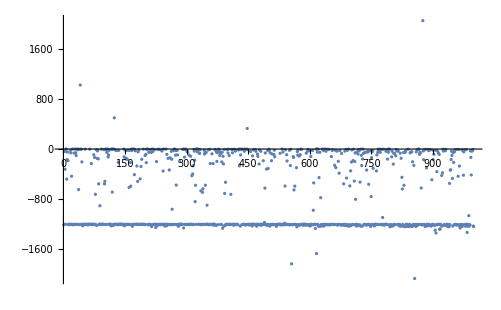

```mathematica
ListPlot[d4⟦All,2⟧]
```

```mathematica
per[nf_,nexplore_,Nv_,ns_,ncompute_]:=(nf nexplore)^Nv (ns nexp+nf ncompute)
```

```mathematica
Solve[per[nf,nexp,Nv,ns,compute]==c,Nv]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Nv→-Log[(compute nf+nexp ns)/c]/Log[nexp nf]}}

```mathematica
nf=10;ncompute = 20; ns = 30;
```

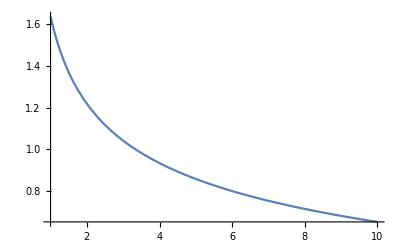

```mathematica
Plot[-Log[(ncompute nf+nexp ns)/10000]/Log[nexp nf],{nexp,1,10}]
```

```mathematica
per[10,50,2,30]
```

300000

```mathematica
per[10,10,3,30]
```

30000000

```mathematica
Solve[(10 250)^1==(10 x)^2,x,Reals]//N
```

{{x→-5.},{x→5.}}

```mathematica
Or[A,B]==Implies[A, Not[B]]/.{A->False,B->True}
```

True